```mathematica
Accretion Models
```

Accretion Models

```mathematica
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]
```

Define the parameters and constants

```mathematica
gamma=1.6;
kboltz=1.381*10^-23;  (*Joule per Kelvin*)
mH2=3.345*10^-27; (*kg*)
muH2=2.72* 1.67*10^-27; (*kg*)

Msun=1.988435*10^30;  (*kg*)
c=299792*10^3; (*m/s*)
G=6.674*10^-11  ;(*N * m^2 * kg^-2  *)


kpc=3.086*10^16 *10^3;(*m*)
cm=10^-2;
cm3=cm^3;
km=10^3;

s=1;
year=3.154*10^7*s
```

3.154×10^7

## Define the model

## Define speed of sound vs T, n

```mathematica
csT[T_]:= Sqrt[gamma*kboltz/mH2*T]/1000;   (*km/s*)
Tcs[cs_]:=(cs*1000)^2*mH2/(gamma*kboltz)
csn[n_]:=3.7*(n/100)^(-0.35);  (*n in cm^-3*)
Tn[n_]:=Tcs[csn[n]]
```

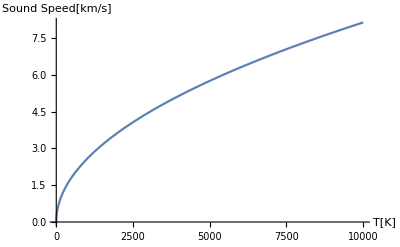

```mathematica
Plot[csT[T], {T,0,10000}, AxesLabel->{"T[K]","Sound Speed[km/s]"}]
```

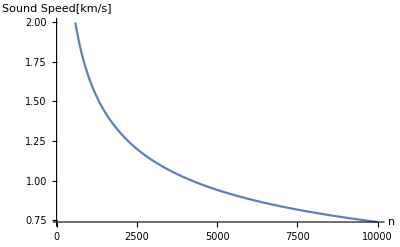

```mathematica
Plot[csn[n], {n,100,10000}, AxesLabel->{"n","Sound Speed[km/s]"}]
```

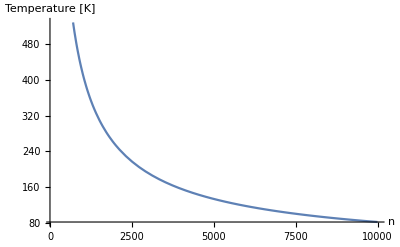

```mathematica
Plot[Tn[n],  {n,100,10000}, AxesLabel->{"n","Temperature [K]"}]
```

## Define Delta T

```mathematica
Deltat[cs_, csin_]:=csin^2/cs^2
```

## Threshold Velocities

```mathematica
MdT[Tout_, Tin_]:=Sqrt[Tin/Tout]*(1-Sqrt[1-(Tout/Tin)])
MrT[Tout_, Tin_]:=Sqrt[Tin/Tout]*(1+Sqrt[1-(Tout/Tin)])
```

```mathematica
Plot[{MdT[T,Tcs[25]], MrT[T, Tcs[25]]}, {T, 1, 10^5}, PlotLabels->{"M_d","M_r"}, AxesLabel->{"T out [K]","Mach"}]
```

-Graphics-

```mathematica
Md[cs_, csin_]:=Sqrt[Deltat[cs, csin]]*(1-Sqrt[1-(1/Deltat[cs, csin])])
Mr[cs_, csin_]:=Sqrt[Deltat[cs, csin]]*(1+Sqrt[1-(1/Deltat[cs, csin])])
```

```mathematica
pl1=Plot[{Md[cs, 25], Mr[cs,25]}, {cs, .1, 30}, PlotLabels->{"M_d","M_r"}, AxesLabel->{"local Sound Speed [km/s]","Mach"}]
```

-Graphics-

```mathematica
pl2=Plot[{Md[c, 10], Mr[c, 10]}, {c, .1, 10}, PlotLabels->{"M_d","M_r"}, AxesLabel->{"local Sound Speed [km/s]","Mach"}]
```

-Graphics-

```mathematica
Show[{pl1, pl2}, PlotLabel->"Mr and Md fos csin = 25 and 10 km/s"]
```

-Graphics-

```mathematica
Plot[{MrT[T],2*Sqrt[ Deltat[csT[T]]]}, {T, 1, 10^5}, PlotLabels->{"M_d","Aprrox"}, AxesLabel->{"T out [K]","Mach"}]
```

-Graphics-

## Delta

```mathematica
Mach[v_, cs_]:=v/cs
Delta[v_, cs_, csin_]:= (1+Mach[v, cs]^2)^2-4*Mach[v, cs]^2*Deltat[cs, csin]
```

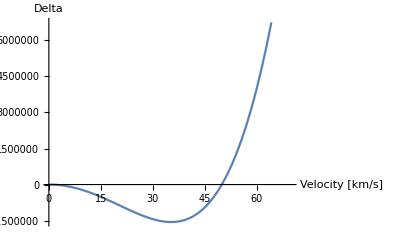

```mathematica
Plot[Delta[v, 1,25], {v,0,70}, AxesLabel->{"Velocity [km/s]","Delta"}]
```

## Delta Rho

```mathematica
vd[cs_, csin_]:=Md[cs, csin]*cs     
vr[cs_, csin_]:=Mr[cs, csin]*cs
```

```mathematica
N[vr[.5,25]]
```

49.995

```mathematica
Deltarhoplus[v_, cs_, csin_]:= (1+Mach[v, cs]^2+Sqrt[Delta[v, cs, csin]])/(2*Deltat[cs, csin])
Deltarhominus[v_, cs_, csin_]:= (1+Mach[v, cs]^2-Sqrt[Delta[v, cs, csin]])/(2*Deltat[cs, csin])
Deltarhozero[v_, cs_, csin_]:= (1+Mach[v, cs]^2)/(2*Deltat[cs, csin])
```

```mathematica
Plot[{Deltarhoplus[v, 1, 10],Deltarhominus[v, 1, 10], Deltarhozero[v, 1, 10]} , {v,0, vd[1,10]},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"}]
```

-Graphics-

```mathematica
Plot[{Deltarhoplus[v, 1, 10],Deltarhominus[v, 1, 10], Deltarhozero[v, 1, 10]} , {v,vr[1,10], 100},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"}]
```

-Graphics-

```mathematica
pl3=Plot[{Deltarhoplus[v, 1, 10],Deltarhominus[v, 1, 10], Deltarhozero[v, 1, 10]} , {v,0, 50},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"}]
```

-Graphics-

```mathematica
pl4=Plot[{Deltarhoplus[v, 1, 12],Deltarhominus[v, 1, 12], Deltarhozero[v, 1, 12]} , {v,0, 50},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"}];
```

```mathematica
Show[{pl3,pl4}, PlotRange->{Automatic,{0,5}}, PlotLabel-> "Delta rho for csin=10 and 12 km/s"]
```

-Graphics-

-Graphics-

```mathematica
Plot[{Deltarhoplus[v, 1,10],Deltarhominus[v, 1, 10], Deltarhozero[v, 1, 10]} , {v,0, 50},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"},  PlotRange->{{0,100},{0,5}}]
```

-Graphics-

```mathematica
Plot[{Deltarhoplus[v, .5, 25],Deltarhominus[v, .5, 25], Deltarhozero[v, .5, 25]} , {v,0, 100},  AxesLabel->{"Velocity [km/s]","Delta Rho plus"},PlotLabels->{"Rho plus ","Rho minus", "Rho zero"},  PlotRange->{{0,100},{0,5}}]
```

-Graphics-

## n inside

```mathematica
ninplus[v_, cs_, n_, csin_]:= Deltarhoplus[v, cs, csin]*n       (*cm^-3*)
ninminus[v_, cs_, n_, csin_]:= Deltarhominus[v, cs, csin]*n
ninzero[v_, cs_, n_, csin_]:= Deltarhozero[v, cs, csin]*n
```

```mathematica
Plot[{ninplus[v, 1, 10^4, 10],ninminus[v, 1, 10^4, 10], ninzero[v, 1, 10^4, 10]}, {v,0,vd[1,10]},  AxesLabel->{"Velocity [km/s]","n in"}, PlotLabels->{"plus ","minus", "zero"}, PlotLabel->"number density in ionized phase"]
```

-Graphics-

```mathematica
Plot[{ninplus[v, 1, 10^4, 10],ninminus[v, 1, 10^4, 10], ninzero[v, 1, 10^4, 10]}, {v,vr[1,10], 100},  AxesLabel->{"Velocity [km/s]","n in"}, PlotLabels->{"plus ","minus", "zero"}, PlotLabel->"number density in ionized phase"]
```

-Graphics-

```mathematica
Plot[{ninplus[v, 1, 10^4, 10],ninminus[v, 1, 10^4, 10], ninzero[v, 1, 10^4, 10]}, {v,0, 50},  AxesLabel->{"Velocity [km/s]","n in"}, PlotLabels->{"plus ","minus", "zero"}, PlotLabel->"number density in ionized phase"]
```

-Graphics-

## v inside (for n out =10^4)

```mathematica
vinplus[v_, cs_, csin_]:= v/Deltarhoplus[v, cs, csin]
vinminus[v_, cs_, csin_]:= v/Deltarhominus[v, cs, csin]
vinzero[v_, cs_, csin_]:= v/Deltarhozero[v, cs, csin]
```

```mathematica
Plot[{vinplus[v, 1, 10],vinminus[v, 1,10], vinzero[v,1,10]}, {v,0,vd[1,10]},  AxesLabel->{"Velocity [km/s]","V in"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
Plot[{vinplus[v, 1,10],vinminus[v, 1, 10], vinzero[v,1, 10]}, {v,0,2},  AxesLabel->{"Velocity [km/s]","V in"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
Plot[{vinplus[v, 1, 10],vinminus[v, 1, 10], vinzero[v,1, 10]}, {v,0, 50},  AxesLabel->{"Velocity [km/s]","V in"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

## Accretion Rate

```mathematica
(*In units of kg/s*)
```

```mathematica
const=G^2* Exp[1.5]*Pi;
```

```mathematica
Mpeakapprox  = const*(7*Msun)^2/(3*25*1000)^3*2*10^4/cm3*muH2
MBondiapprox= const*(7*Msun)^2/(50*1000)^3*10^4/cm3*muH2
Mdotzero[vr[1,25],10^4, 7*Msun, 1,25]
```

2.61646×10^12

4.41528×10^12

Mdotzero[25 (1+(4 √39)/25),10000,1.3919×10^31,1,25]

```mathematica
rhoinplus[v_,  n_,cs_, csin_]:= ninplus[v,cs, n, csin]/cm3*muH2
rhoinminus[v_,  n_,cs_, csin_]:= ninminus[v,cs, n, csin]/cm3*muH2
rhoinzero[v_,  n_,cs_, csin_]:= ninzero[v, cs, n, csin]/cm3*muH2
```

```mathematica
Mdotplus[v_,  n_,M_, cs_:1, csin_:25]  := const* M^2*((  vinplus[v, cs, csin]*km/s)^2+(csin*km/s)^2)^(-3/2)*rhoinplus[v,n,cs,  csin]
Mdotminus[v_,  n_,M_,  cs_:1, csin_:25] := const*M^2*((vinminus[v, cs, csin]*km/s)^2+(csin*km/s)^2)^(-3/2)*rhoinminus[v, n,cs, csin]
Mdotzero[v_,  n_,M_,  cs_:1, csin_:25]  := const*M^2*((   vinzero[v, cs, csin]*km/s)^2+(csin*km/s)^2)^(-3/2)*rhoinzero[v,  n,cs, csin]
```

```mathematica
Plot[{Mdotplus[v,10^4, 7*Msun, 1, 25],Mdotminus[v,10^4, 7*Msun, 1,25], Mdotzero[v,10^4, 7*Msun, 1, 25]},{v,0,vd[1,25]}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
P3=Plot[{Mdotplus[v,10^4, 7*Msun, .5, 10],Mdotminus[v,10^4, 7*Msun, .5, 10], Mdotzero[v,10^4, 7*Msun, .5, 10]},{v,0,.1}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
LogPlot[{Mdotplus[v,10^4, 7*Msun, .5, 10],Mdotminus[v,10^4, 7*Msun, .5, 10], Mdotzero[v,10^4, 7*Msun, .5, 10]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot [kg/s]"}, PlotLabels->{"plus ","minus", "zero"}, PlotRange->Automatic]
```

-Graphics-

```mathematica
LogPlot[{Mdotplus[v, 10^4,7*Msun]/(Msun/year),Mdotminus[v, 10^4, 7*Msun]/(Msun/year), Mdotzero[v, 10^4, 7*Msun]/(Msun/year)},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot [Msun/year]"}, PlotLabels->{"plus ","minus", "zero"}, PlotRange->Automatic, PlotLabel->"Accretion Rate"]
```

-Graphics-

```mathematica
Mdot[v_, n_,M_,  cs_:1, csin_:25]:=Piecewise[{{Mdotplus[v, n,M, cs, csin], v< vd[cs,csin]}, {Mdotzero[v, n,M, cs, csin], vd[cs,csin]<=v<=vr[cs,csin]}, {Mdotminus[v, n,M, cs, csin], v>= vr[cs,csin]}}]
```

## Impact of n and cs on accretion rate

```mathematica
P1=Plot[{Mdotplus[v,10^4, 7*Msun, .5, 10],Mdotminus[v,10^4, 7*Msun, .5, 10], Mdotzero[v,10^4, 7*Msun, .5, 10]},{v,0,30}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"},  PlotRange->{{0,30},Automatic}]
```

-Graphics-

```mathematica
P2=Plot[{Mdotplus[v,10^4, 7*Msun, 1, 10],Mdotminus[v,10^4, 7*Msun, 1, 10], Mdotzero[v,10^4, 7*Msun, 1, 10]},{v,0,30}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"},  PlotRange->{{0,30},Automatic}]
```

-Graphics-

```mathematica
Show[{P1,P2},  PlotLabel->" cs=.5 vs cs=1 for high velocity "]
```

-Graphics-

```mathematica
P4=Plot[{Mdotplus[v,10^4, 7*Msun, 1, 10],Mdotminus[v,10^4, 7*Msun, 1, 10], Mdotzero[v,10^4, 7*Msun, 1, 10]},{v,0,.1}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
Show[{P3, P4} ,  PlotLabel->"cs=.5 vs cs=1 for low velocity"]
```

-Graphics-

```mathematica
P5=Plot[{Mdotplus[v,10^3, 7*Msun, .5, 10],Mdotminus[v,10^3, 7*Msun, .5, 10], Mdotzero[v,10^3, 7*Msun, .5, 10]},{v,0,30}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"},  PlotRange->{Automatic,Automatic}]
```

-Graphics-

```mathematica
Show[{P1, P5},   PlotLabel->"n=10^4 vs n=10^3 "]
```

-Graphics-

```mathematica
Plot[{Mdotplus[vr[1,25], n, 7*Msun],Mdotminus[vr[1,25], n, 7*Msun], Mdotzero[vr[1, 25],  n,7*Msun]},{n,10^2,10^4}, AxesLabel->{"n","Mdot"}, PlotLabels->{"plus ","minus", "zero"},  PlotRange->{{10,10000},Automatic},   PlotLabel->"Peak accretion vs n for cs=1 km/s"]
```

-Graphics-

```mathematica
Plot[{Mdotplus[50,  n, 7*Msun],Mdotminus[50,  n,7*Msun], Mdotzero[50,  n,7*Msun]},{n,10^2,10^4}, AxesLabel->{"n","Mdot"}, PlotLabels->{"plus ","minus", "zero"},   PlotLabel->"accretion vs rho for v=50 kms, cs=1 km/s"]
```

-Graphics-

```mathematica
(*derivatives*)
D[Mdotzero[10,  n, 7*Msun], n]   
D[Mdotzero[vr[.5,10], n, 7*Msun], n]
D[Mdotminus[50,n, 7*Msun], n]
```

2.21544×10^6

5.82557×10^7

2.32576×10^9

```mathematica
Plot[{ Mdotzero[vr[cs,10], 10^4, 7*Msun,  cs],  Mdotzero[vr[cs,10], 10^3, 7*Msun,  cs]},{cs,.1,10}, AxesLabel->{"n","Mdot"}, PlotLabels->{"10^4", "10^3"},  PlotRange->{Automatic,Automatic},   PlotLabel->"Peak accretion vs cs for n= 10^4, 10^3"]
```

-Graphics-

## Impact of Ionized Sound Speed on Accretion Rate

```mathematica
P6=LogPlot[{Mdotplus[v,10^4, 7*Msun, 1, 10],Mdotminus[v,10^4, 7*Msun, 1, 10], Mdotzero[v,10^4, 7*Msun, 1, 10]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
P7=LogPlot[{Mdotplus[v,10^4, 7*Msun, 1, 25],Mdotminus[v,10^4, 7*Msun, 1, 25], Mdotzero[v,10^4, 7*Msun, 1, 25]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero"}]
```

-Graphics-

```mathematica
Show[{P6,P7}, PlotLabel-> "Accretion Rate for csin= 10 and 25 km/s"]
```

-Graphics-

## Comparison with Bondi accretion

```mathematica
MdotBondi[v_,  n_, M_,cs_:1]:= const*M^2*((v*km)^2+(cs*km)^2)^(-3/2)*n/cm3*muH2
```

```mathematica
Plot[{Mdotplus[v, 10^4, 7*Msun],Mdotminus[v, 10^4, 7*Msun], Mdotzero[v,  10^4,7*Msun],  MdotBondi[v, 10^4, 7*Msun]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"Bondi accretion vs Ricotti for n= 10^4"]
```

-Graphics-

```mathematica
LogPlot[{Mdotplus[v, 10^4, 7*Msun],Mdotminus[v, 10^4, 7*Msun], Mdotzero[v,  10^4,7*Msun],  MdotBondi[v, 10^4, 7*Msun]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"Bondi accretion vs Ricotti for n= 10^4"]
```

-Graphics-

```mathematica
LogPlot[{Mdotplus[v, 10^3, 7*Msun],Mdotminus[v, 10^3, 7*Msun], Mdotzero[v,  10^3,7*Msun],  MdotBondi[v, 10^3, 7*Msun]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Mdot"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"Bondi accretion vs Ricotti for n= 10^3"]
```

-Graphics-

## Luminosity

```mathematica
(*Luminosity in J/s*)
```

```mathematica
eta0=0.1;
(*s=-1.6;
R=Integrate[x^s, {x,10,40}]/Integrate[x^s, {x,2,10}]*)
```

```mathematica
LEddFender= 1.26*10^31* 7;
LEdd[M_]:=1.26*10^31* (M/Msun) (*J/s*)

Mdotcrit[M_]:= 0.01*LEdd[M]/(eta0*c^2)

eta[Mdot_, M_]:= eta0*Mdot/Mdotcrit[M]

LogPlot[{eta[Mdotplus[v,10^4, 7*Msun], 7*Msun],eta[Mdotminus[v,10^4, 7*Msun], 7*Msun],eta[Mdotzero[v,10^4, 7*Msun], 7*Msun]}, {v, 0, 100}, AxesLabel->{"Velocity [km/s]","eta"}, PlotLabels->{"plus ","minus", "zero"}, PlotRange->{Automatic, {0.001, .1}}]
```

-Graphics-

```mathematica
LX[Mdot_, M_, k_]:=k*eta[Mdot,M]*Mdot*c^2
```

```mathematica
(* flux in J/s/m^2 *)
```

```mathematica
Fxminus[v_, n_, M_,d_, cs_:1, csin_:25, k_:0.3]:=LX[Mdotminus[v, n, M, cs, csin], M, k]/(4*Pi*d^2)
Fxplus[v_, n_, M_,d_, cs_:1, csin_:25, k_:0.3]:=LX[Mdotplus[v, n, M, cs, csin], M, k]/(4*Pi*d^2)
Fxzero[v_, n_, M_,d_, cs_:1, csin_:25, k_:0.3]:=LX[Mdotzero[v, n, M, cs, csin], M, k]/(4*Pi*d^2)
FxBondi[v_, n_, M_,d_, cs_:1, csin_:25, k_:0.3]:=LX[MdotBondi[v, n, M, cs], M, k]/(4*Pi*d^2)
```

```mathematica
(*debug*)
Mdotcrit[7*Msun]
Mdotzero[50, 10^4, 7*Msun]
eta[Mdotzero[50, 10^4, 7*Msun], 7*Msun]
LX[Mdotzero[50, 10^4, 7*Msun, 1, 25], 7*Msun]
LX[Mdotzero[50, 10^4, 7*Msun], 7*Msun]
LX[Mdotzero[50, 10^4, 7*Msun], 7*Msun]/(4*Pi*(8*kpc)^2)
Fxzero[50, 10^4, 7*Msun, 8*kpc]
Fxzero[50, 10^4, 7*Msun, 8*kpc, 1, 25]
```

9.8136×10^13

2.50016×10^13

0.0254764

LX[2.50016×10^13,1.3919×10^31]

LX[2.50016×10^13,1.3919×10^31]

1.30562×10^-42 LX[2.50016×10^13,1.3919×10^31]

2.24226×10^-14

2.24226×10^-14

```mathematica
LX[Mdotzero[50, 10^4, 7*Msun, 1, 25], 7*Msun]/LEdd[7*Msun]
```

1.13379×10^-32 LX[2.50016×10^13,1.3919×10^31]

```mathematica
Mdotzero[50,10^4, 7*Msun]/Mdotcrit[7*Msun]
```

0.254764

```mathematica
LogPlot[{Fxplus[v, 10^4,7*Msun, 8*kpc],Fxminus[v, 10^4,7*Msun, 8*kpc], Fxzero[v, 10^4,7*Msun, 8*kpc], FxBondi[v, 10^4,7*Msun, 8*kpc]},{v,0,100}, AxesLabel->{"Velocity [km/s]","Flux[J/s/m^2]"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"Bondi accretion vs Ricotti for n= 10^4"]
```

-Graphics-

```mathematica
(*convert from J/s/m^2 to cgs, ie erg/s/cm^2*)
erg=10^-7;
```

```mathematica
LogPlot[{Fxplus[v, 10^4,7*Msun, 8*kpc]/(erg/cm^2),Fxminus[v, 10^4,7*Msun, 8*kpc]/(erg/cm^2), Fxzero[v, 10^4,7*Msun, 8*kpc]/(erg/cm^2), FxBondi[v, 10^4,7*Msun, 8*kpc]/(erg/cm^2)},{v,10,400}, PlotRange->{Automatic, {10^-20, 10^-8}}, AxesLabel->{"Velocity [km/s]","Flux[erg/s/cm^2]"}, PlotLabels->{"plus ","minus", "zero", "Bondi"}, PlotLabel->"X-ray Flux for n= 10^4"]
```

-Graphics-

## Define the Flux piecewise

```mathematica
Flux[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=Piecewise[{{Fxplus[v, n,M, d, cs, csin, k], v< vd[cs,csin]}, {Fxzero[v, n,M, d, cs, csin, k], vd[cs,csin]<=v<=vr[cs,csin]}, {Fxminus[v, n,M, d, cs, csin, k], v>= vr[cs,csin]}}]
```

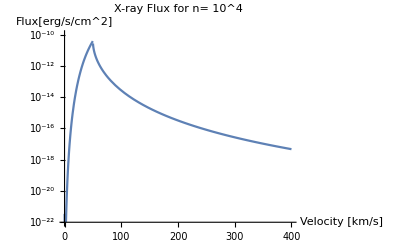

```mathematica
LogPlot[Flux[v, 10^4,8.4*Msun, 8*kpc]/(erg/cm^2), {v,0,400}, AxesLabel->{"Velocity [km/s]","Flux[erg/s/cm^2]"}, PlotLabel->"X-ray Flux for n= 10^4", PlotRange->{Automatic, {10^-22, 10^-10}}]
```

```mathematica
Flux[150, 10^3,7*Msun, 8.3, 1, 25]
```

9.80833×10^18

## Define the Radio Flux using the fundamental plane

```mathematica
Lx[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:= Flux[v, n,M, d, cs, csin, k]*(4*Pi*d^2)
```

Using the fundamental plane values for luminosities in ergs. Must convert to erg and then back to Joules.

```mathematica
a1=1.45;
a2=0.88;
a3=6.07;
```

```mathematica
Lr[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=10^((Log[10, Lx[v, n,M, d, cs, csin, k]/erg]+a2*Log[10, M/Msun]+a3)/a1)*erg;
LrBondi[v_, n_,M_, cs_:1,  k_:0.3]:=10^((Log[10, LX[MdotBondi[v, n, M, cs], M, k]/erg]+a2*Log[10, M/Msun]+a3)/a1)*erg;
```

This is in Joules/s/m^2:

```mathematica
RFlux1[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=Lr[v, n,M, d, cs, csin, k]/(4*Pi*(d)^2);
RFlux1Bondi[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=LrBondi[v, n,M,  cs,  k]/(4*Pi*(d)^2);
```

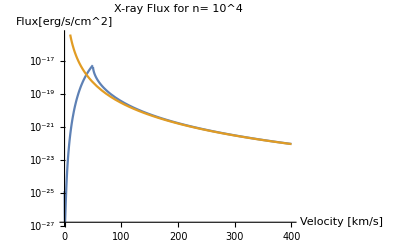

```mathematica
LogPlot[{ RFlux1[v, 10^4,5*Msun, 8*kpc]/(erg/cm^2), RFlux1Bondi[v, 10^4,5*Msun, 8*kpc]/(erg/cm^2)}, {v,0,400}, AxesLabel->{"Velocity [km/s]","Flux[erg/s/cm^2]"}, PlotLabel->"X-ray Flux for n= 10^4"]
```

Convert to mJy (first to erg/cm^2 then to mJy)

```mathematica
obsFrequency=1.4*10^9;
Jyergconversion=10^-23;
```

```mathematica
RFlux[v_, n_,M_, d_, cs_:1, csin_:25, k_:0.3]:=RFlux1[v, n,M, d, cs, csin, k]/(erg/cm^2)*1000/obsFrequency/Jyergconversion
RFluxBondi[v_, n_,M_, d_, cs_:1, k_:0.3]:=RFlux1Bondi[v, n,M, d, cs,  k]/(erg/cm^2)*1000/obsFrequency/Jyergconversion
```

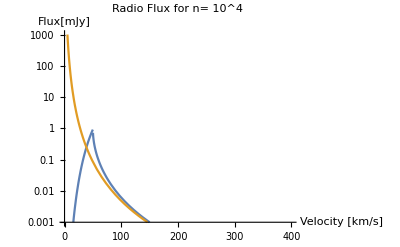

```mathematica
LogPlot[{ RFlux[v, 10^4,7*Msun, 8*kpc], RFluxBondi[v, 10^4,7*Msun, 8*kpc]}, {v,0,400}, AxesLabel->{"Velocity [km/s]","Flux[mJy]"}, PlotLabel->"Radio Flux for n= 10^4", PlotRange->{Automatic, {10^-3, 10^3}}]
```

Compare X and Radio bands

```mathematica
LogPlot[{ RFlux1[v, 10^4,5*Msun, 8*kpc]/(erg/cm^2), Flux[v, 10^4,5*Msun, 8*kpc]/(erg/cm^2)}, {v,0,400}, AxesLabel->{"Velocity [km/s]","Flux[erg/s/cm^2]"}, PlotLabel->"X-ray vs Radio Flux for n= 10^4", PlotLabels->{"Radio", "Xray"}]
```

-Graphics-

## Apply the model to ABHs

## Plot dependence of accretion rate on parameters

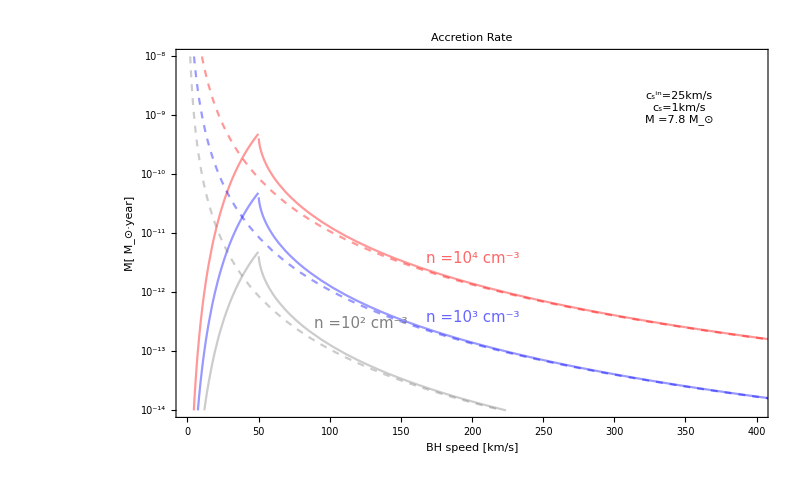

```mathematica
Legended[
LogPlot[
{
Mdot[v, 10^4,7.8*Msun]/(Msun/year),Mdot[v, 10^3,7.8*Msun]/(Msun/year), Mdot[v, 10^2,7.8*Msun]/(Msun/year),
MdotBondi[v, 10^4,7.8*Msun]/(Msun/year),MdotBondi[v, 10^3,7.8*Msun]/(Msun/year), MdotBondi[v, 10^2,7.8*Msun]/(Msun/year)},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-14, 10^-8}},
PlotLabel->AccretionTitle,
FrameLabel->{labelv,labelMdot}, 
ImageSize->800, 
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;3]],Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[1;;3]]],
FrameTicks->{{ticksMdot, None},{ticksv, None}},
PlotLabels->Placed[{DisplayForm[StyleBox[ntext[4], MyColors[[1]], Opacity[.6]]],DisplayForm[StyleBox[ntext[3],  MyColors[[2]], Opacity[.6]]], DisplayForm[StyleBox[ntext[2],  MyColors[[3]], Opacity[1]]]},Scaled[.4]]
],

{ Placed[Framed[Column[{csintext[25],cstext[1],  Mtext[7.8]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.4}]
}
]
```

```mathematica
DisplayForm[StyleBox[ntext[4], MyColors[[1]], Opacity[.1]]]
```

n =10^4 cm^-3

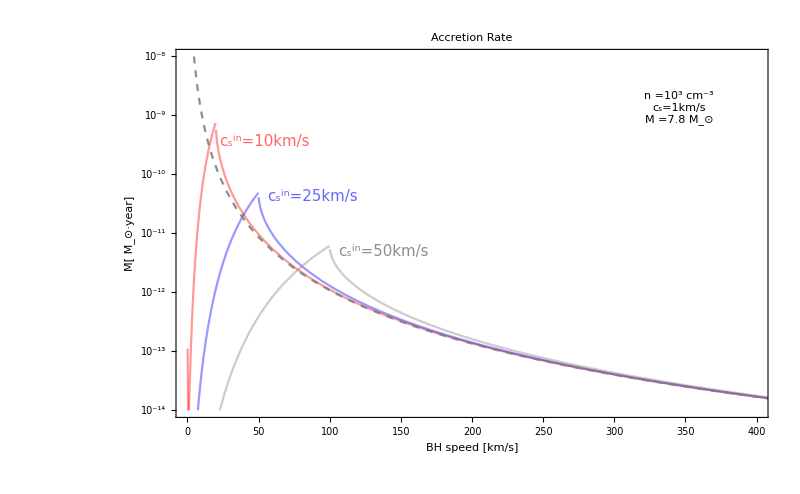

```mathematica
Legended[
LogPlot[
{
Mdot[v, 10^3,7.8*Msun, 1, 10]/(Msun/year),Mdot[v, 10^3,7.8*Msun, 1, 25]/(Msun/year), Mdot[v, 10^3,7.8*Msun, 1, 50]/(Msun/year),
MdotBondi[v, 10^3,7.8*Msun]/(Msun/year)},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-14, 10^-8}},
PlotLabel->AccretionTitle,
FrameLabel->{labelv,labelMdot}, 
ImageSize->800, 
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;3]],{Directive[Gray, Opacity[.9], Dashed]}],
FrameTicks->{{ticksMdot, None},{ticksv, None}}
],

{ 

Placed[Framed[Column[{ntext[3],cstext[1],  Mtext[7.8]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.4}],

Placed[DisplayForm[StyleBox[csintext[10], MyColors[[1]], Opacity[.6]]], {.15, .75}],
Placed[DisplayForm[StyleBox[csintext[25], MyColors[[2]], Opacity[.6]]], {.23, .6}],
Placed[DisplayForm[StyleBox[csintext[50], MyColors[[3]], Opacity[.9]]], {.35, .45}]
}
]
```

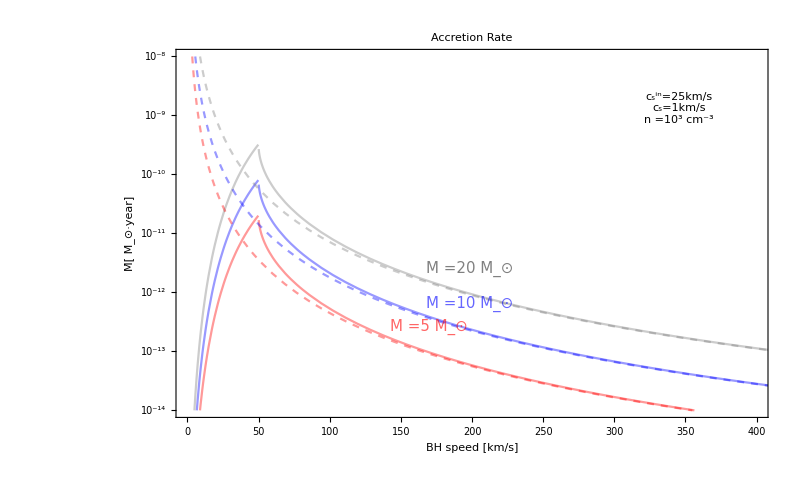

```mathematica
Legended[
LogPlot[
{
Mdot[v, 10^3,5*Msun]/(Msun/year),Mdot[v, 10^3,10*Msun]/(Msun/year), Mdot[v, 10^3,20*Msun]/(Msun/year),
MdotBondi[v, 10^3,5*Msun]/(Msun/year),MdotBondi[v, 10^3,10*Msun]/(Msun/year), MdotBondi[v, 10^3,20*Msun]/(Msun/year)},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-14, 10^-8}},
PlotLabel->AccretionTitle,
FrameLabel->{labelv,labelMdot}, 
ImageSize->800, 
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;3]],Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[1;;3]]],
FrameTicks->{{ticksMdot, None},{ticksv, None}},
PlotLabels->Placed[{DisplayForm[StyleBox[Mtext[5], MyColors[[1]], Opacity[.6]]],DisplayForm[StyleBox[Mtext[10],  MyColors[[2]], Opacity[.6]]], DisplayForm[StyleBox[Mtext[20],  MyColors[[3]], Opacity[1]]]},Scaled[.4]]
],

{ Placed[Framed[Column[{csintext[25],cstext[1],  ntext[3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.4}]
}
]
```

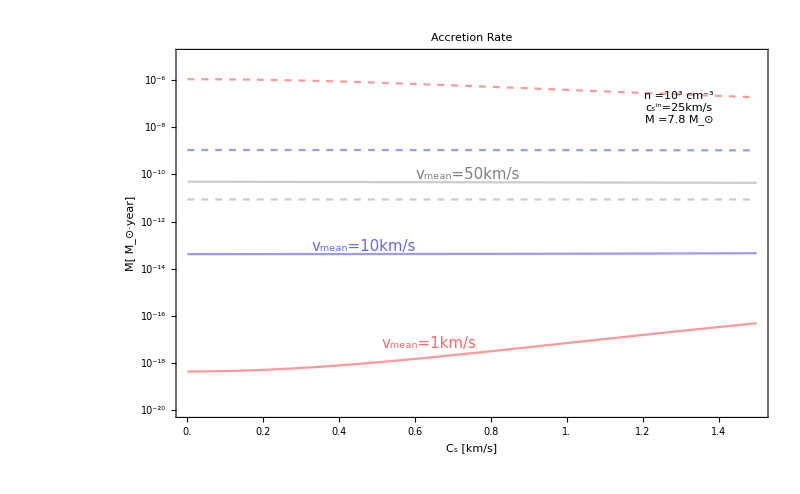

```mathematica
Legended[
LogPlot[
{
Mdot[1, 10^3,7.8*Msun, cs, 25]/(Msun/year),Mdot[10, 10^3,7.8*Msun, cs, 25]/(Msun/year), Mdot[50, 10^3,7.8*Msun, cs, 25]/(Msun/year),
MdotBondi[1, 10^3,7.8*Msun, cs]/(Msun/year),MdotBondi[10, 10^3,7.8*Msun, cs]/(Msun/year), MdotBondi[50, 10^3,7.8*Msun, cs]/(Msun/year)},
{cs,0,1.5}, 
Frame->True,
PlotRange->{{0,1.5},{10^-20, 10^-5}},
PlotLabel->AccretionTitle,
FrameLabel->{labelcs,labelMdot}, 
ImageSize->800, 
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;3]],Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[1;;3]]],
FrameTicks->{{ticksF, None},{tickscs, None}},
GridLines->{Table[50*i,{i,40}],Automatic},
PlotLabels->Placed[{DisplayForm[StyleBox[vtext[1], MyColors[[1]], Opacity[.6]]],DisplayForm[StyleBox[vtext[10],  MyColors[[2]], Opacity[.6]]], DisplayForm[StyleBox[vtext[50],  MyColors[[3]], Opacity[1]]]},Scaled[.4]]
],

{ 
Placed[Framed[Column[{ntext[3],csintext[25],  Mtext[7.8]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.2}]

}
]
```

```mathematica
Legended[
LogPlot[
{
Mdot[v, 10^3,5*Msun, 1, 25]/(Msun/year),Mdot[v, 10^3,10*Msun, 1, 25]/(Msun/year), Mdot[v, 10^3,15*Msun, 1, 25]/(Msun/year),
MdotBondi[v, 10^3,5*Msun, 1]/(Msun/year),MdotBondi[v, 10^3,10*Msun, 1]/(Msun/year), MdotBondi[v, 10^3,15*Msun, 1]/(Msun/year)},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-14, 10^-8}},
PlotLabel->AccretionTitle,
FrameLabel->{labelv,labelMdot}, 
ImageSize->800, 
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;3]],Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[1;;3]]],
FrameTicks->{{ticksF, None},{ticksv, None}},
GridLines->{Table[50*i,{i,40}],Automatic},
PlotLabels->Placed[{DisplayForm[StyleBox[Mtext[5], MyColors[[1]], Opacity[.6]]],DisplayForm[StyleBox[Mtext[10],  MyColors[[2]], Opacity[.6]]], DisplayForm[StyleBox[Mtext[15],  MyColors[[3]], Opacity[1]]]},Scaled[.5]]
],

{ 
Placed[csintext[25], {.85, .92}],
Placed[ntext[3], {.85, .80}],
Placed[cstext[1], {.85, .86}],
 Placed[LineLegend[{{Gray, Dashed}, Gray},{labelBondi1 ,labelRicotti}], 
{.85,.6}]
}
]
```

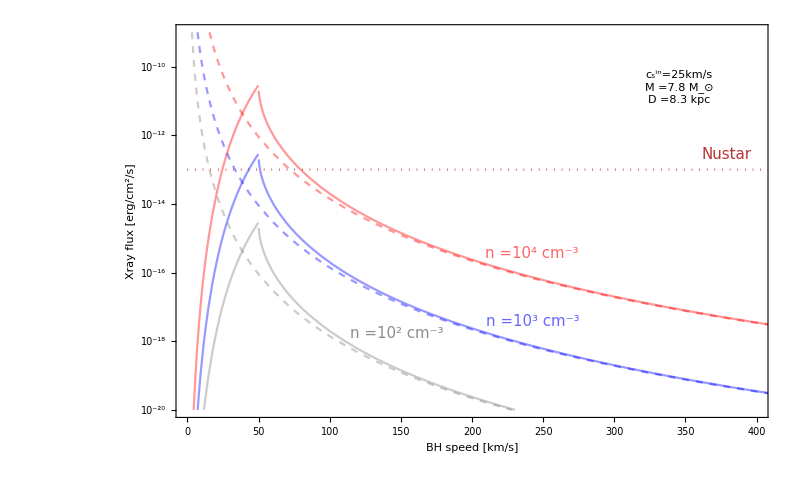

```mathematica
Legended[
LogPlot[
{
Flux[v, 10^4,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),Flux[v, 10^3,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2), Flux[v, 10^2,7.8*Msun,8.3*kpc, 1]/(erg/cm^2),
FxBondi[v, 10^4,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),FxBondi[v, 10^3,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2), FxBondi[v, 10^2,7.8*Msun,8.3*kpc, 1]/(erg/cm^2),
Nustarsensitivity},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-20, 10^-9}},
FrameLabel->{labelv,labelXflux}, 
ImageSize->800, 
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;3]],Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[1;;3]], {Directive[Darker[Red],Dotted,  Opacity[.8]]}],
FrameTicks->{{ticksF, None},{ticksv, None}},
PlotLabels->Placed[{DisplayForm[StyleBox[ntext[4], MyColors[[1]], Opacity[.6]]],DisplayForm[StyleBox[ntext[3],  MyColors[[2]], Opacity[.6]]], DisplayForm[StyleBox[ntext[2],  MyColors[[3]], Opacity[.9]]]},Scaled[.5]]
],

{ Placed[NustarText, {.93,.67}],
Placed[Framed[Column[{csintext[25], Mtext[7.8],dtext[8.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.4}]
}
]
```

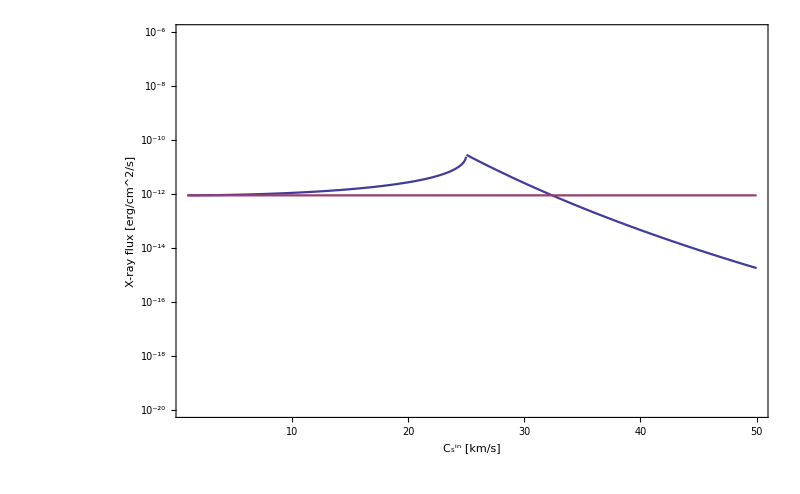

```mathematica
Legended[
LogPlot[
{Flux[50, 10^4,7.8*Msun, 8.3*kpc, 1, csin]/(erg/cm^2),
FxBondi[50, 10^4,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2)
},
{csin,1,50}, 
Frame->True,
PlotRange->{{1,50},{10^-20, 10^-6}},
FrameLabel->{labelcsin,labelXflux}, 
ImageSize->800, 
PlotStyle->ColorData[1,"ColorList"],
FrameTicks->{{ticksF, None},{tickscsin, None}},
GridLines->{Automatic,Automatic}
],
 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"Ricotti" ,"Bondi"}],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

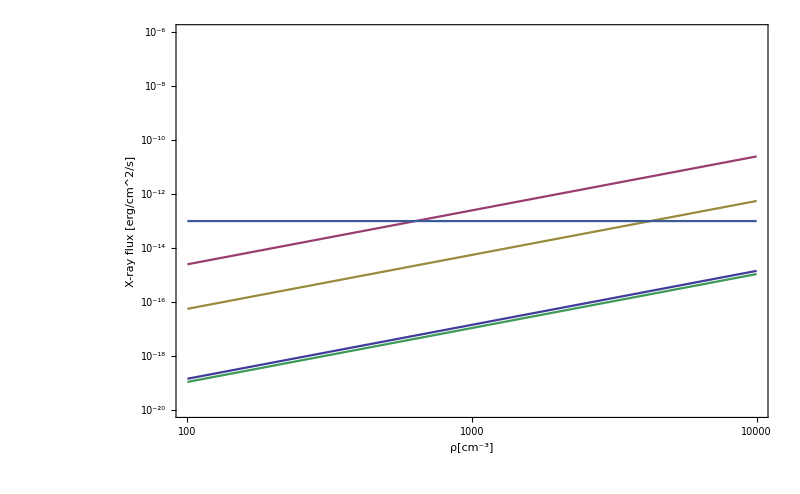

```mathematica
Legended[
LogLogPlot[

{Flux[150,rho ,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),
Flux[50,rho ,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),
Flux[30,rho ,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),
Flux[15,rho ,7.8*Msun, 8.3*kpc, 1]/(erg/cm^2),

Nustarsensitivity
},
{rho,10^2,10^4}, 
Frame->True,
PlotRange->{{10^2,10^4},{10^-20, 10^-6}},
PlotStyle->ColorData[1,"ColorList"],
FrameLabel->{labelrho,labelXflux}, 
ImageSize->800, 
PlotStyle->{{Automatic}},
FrameTicks->{{ticksF, None},{ticksrho, None}},
GridLines->{Automatic,Automatic}
],
 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"v= 150 km/s","v= 50 km/s" ,"v= 30 km/s" ,"v= 15 km/s" }],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

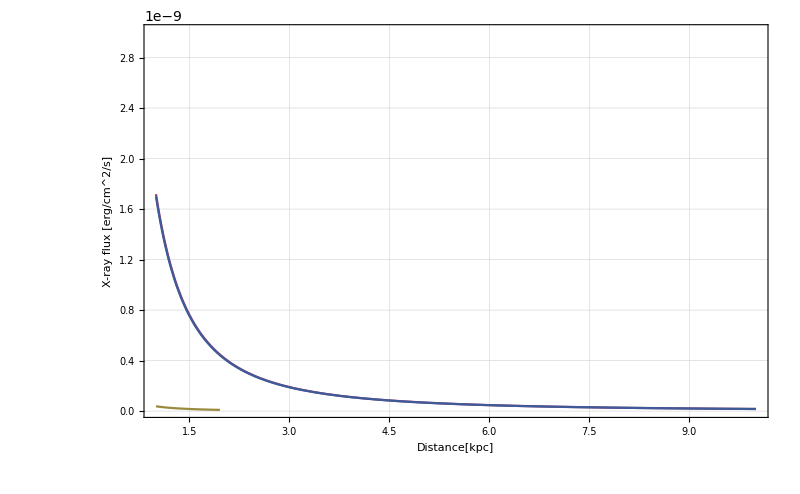

```mathematica
Legended[
Plot[

{Flux[150,10^4 ,7.8*Msun, d*kpc, 1]/(erg/cm^2),
Flux[50,10^4 ,7.8*Msun, d*kpc, 1]/(erg/cm^2),
Flux[30,10^4 ,7.8*Msun, d*kpc, 1]/(erg/cm^2),
Flux[15,10^4,7.8*Msun, d*kpc, 1]/(erg/cm^2),
1.7*10^-9*d^-2
},
{d,1,10}, 
Frame->True,
PlotRange->{{1,10},{10^-11, 3*10^-9}},
PlotStyle->ColorData[1,"ColorList"],
FrameLabel->{labeld,labelXflux}, 
ImageSize->800, 
PlotStyle->{{Automatic}},
FrameTicks->{{Automatic, None},{Automatic, None}},
GridLines->{Automatic,Automatic}
],
 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"v= 150 km/s","v= 50 km/s" ,"v= 30 km/s" ,"v= 15 km/s" }],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

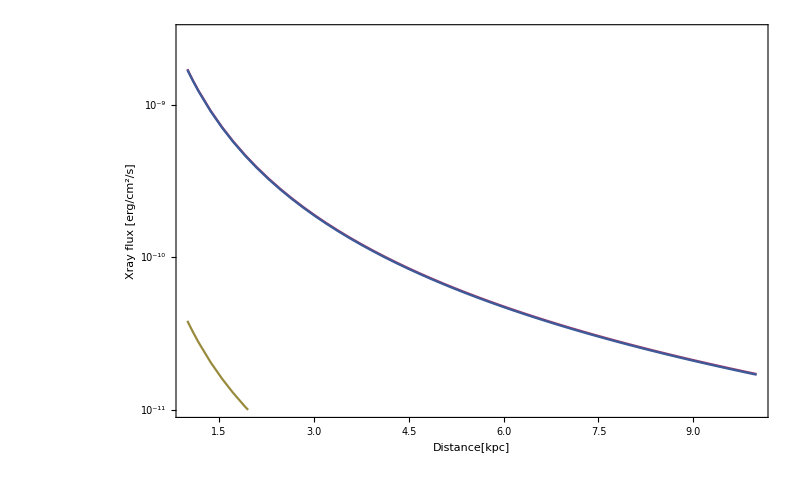

```mathematica
Legended[
LogPlot[

{Flux[150,10^4 ,7.8*Msun, d*kpc, 1]/(erg/cm^2),
Flux[50,10^4 ,7.8*Msun, d*kpc, 1]/(erg/cm^2),
Flux[30,10^4 ,7.8*Msun, d*kpc, 1]/(erg/cm^2),
Flux[15,10^4,7.8*Msun, d*kpc, 1]/(erg/cm^2),
1.7*10^-9*d^-2
},
{d,1,10}, 
Frame->True,
PlotRange->{{1,10},{10^-11, 3*10^-9}},
PlotStyle->ColorData[1,"ColorList"],
FrameLabel->{labeld,labelXflux}, 
ImageSize->800, 
PlotStyle->{{Automatic}},
FrameTicks->{{Automatic, None},{Automatic, None}},
GridLines->{Automatic,Automatic}
],
 Placed[Framed
[LineLegend[ColorData[1,"ColorList"],{"v= 150 km/s","v= 50 km/s" ,"v= 30 km/s" ,"v= 15 km/s" }],
Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.85}]
]
```

## Plot accretion rate vs velocity

### X-ray flux from CMZ clouds

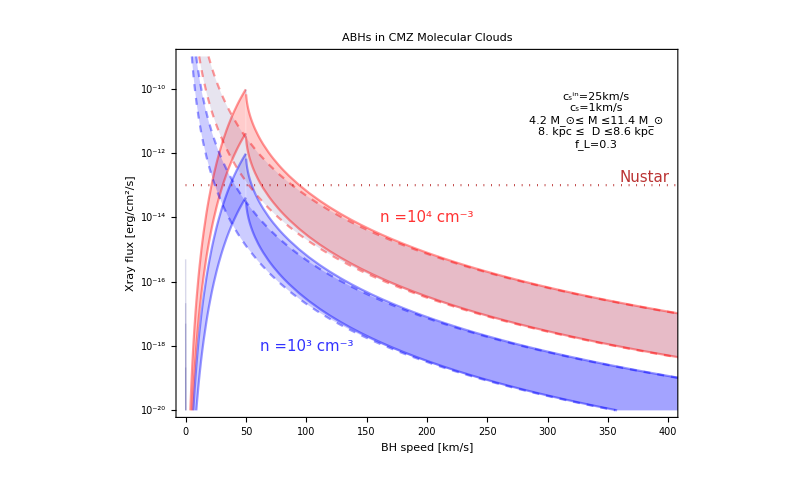

```mathematica
LogPlot[
{
Flux[v, 10^4,Mmin, Dmax]/(erg/cm^2), Flux[v, 10^4,Mmax, Dmin]/(erg/cm^2), 
Flux[v, 10^3,Mmin, Dmax]/(erg/cm^2), Flux[v, 10^3,Mmax, Dmin]/(erg/cm^2),
FxBondi[v, 10^4,Mmin, Dmax]/(erg/cm^2), FxBondi[v, 10^4,Mmax, Dmin]/(erg/cm^2), 
FxBondi[v, 10^3,Mmin, Dmax]/(erg/cm^2), FxBondi[v, 10^3,Mmax, Dmin]/(erg/cm^2),
Nustarsensitivity },
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-20, 10^-9}},
FrameLabel->{labelv,labelXflux}, 
PlotLabel->CMZTitle,
ImageSize->800, 
PlotStyle->Join[
Table[{MyColors[[1]], Opacity[.4]}, {i,2}],Table[{MyColors[[2]], Opacity[.4]}, {i,2}], 
Table[{MyColors[[1]], Opacity[.4], Dashed}, {i,2}],Table[{MyColors[[2]], Opacity[.4], Dashed}, {i,2}], 
{Directive [Darker[Red], Dotted]}], 
Filling->Table[2*i-1->{2*i}, {i,4}],
FrameTicks->{{ticksF, None},{ticksv, None}},
Epilog->{
Text[DisplayForm[StyleBox[ntext[4], MyColors[[1]], Opacity[.8], FontSize->20]],{200, Log[10^-14]}],
Text[DisplayForm[StyleBox[ntext[3], MyColors[[2]], Opacity[.8], FontSize->20]],{100, Log[10^-18]}],
Text[NustarText, {380,Log[10^-13]}, {0, -1.5}],
Text[Framed[Column[{csintext[25],cstext[1], Mtext2[Mmin/Msun, Mmax/Msun],dtext2[Dmin/kpc, Dmax/kpc], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {340, Log[10^-11]}],
Text[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{340,Log[10^-15]}]
}
]
```

#### Rough estimate of sources above threshold. Assuming around 3000 BH in the most dense CMZ clouds. Including velocities between 35 and 60 km/s.

```mathematica
N[130/Sqrt[8/Pi]]
N[75/Sqrt[8/Pi]]
```

81.4654

46.9993

```mathematica
sigmav=Sqrt[80^2+50^2]
pofv[x_]:=PDF[MaxwellDistribution[sigmav], x];
```

10 √89

```mathematica
N[sigmav]
```

94.3398

```mathematica
vminCMZ=35;
vmaxCMZ=60;
```

```mathematica
N[Integrate[Pofv[x], {x,vminCMZ,vmaxCMZ}]]
```

0.0480529

### X-ray flux from the nearest black holes, following Fender & Maccarone

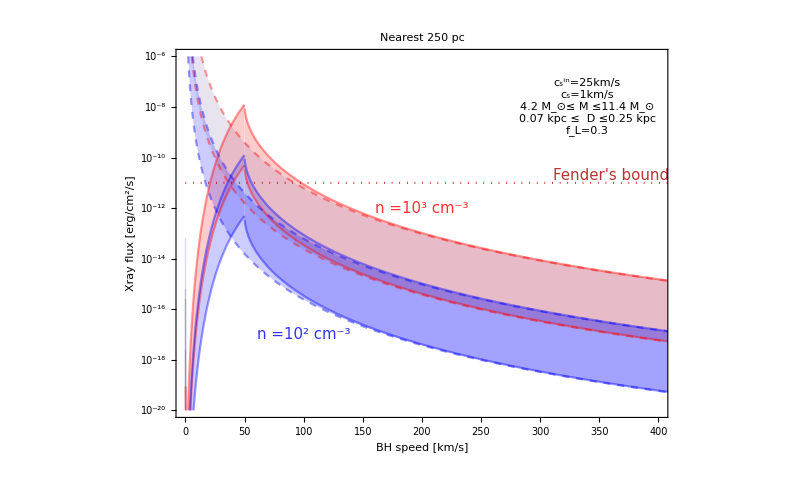

```mathematica
LogPlot[{
Flux[v, 10^3,Mmin, DFmax]/(erg/cm^2), Flux[v, 10^3,Mmax, DFmin]/(erg/cm^2), 
Flux[v, 10^2,Mmin, DFmax]/(erg/cm^2), Flux[v, 10^2,Mmax, DFmin]/(erg/cm^2),
FxBondi[v, 10^3,Mmin, DFmax]/(erg/cm^2),FxBondi[v, 10^3,Mmax, DFmin]/(erg/cm^2),
FxBondi[v, 10^2,Mmin, DFmax]/(erg/cm^2), FxBondi[v, 10^2,Mmax, DFmin]/(erg/cm^2),
FendersensitivityX },
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-20, 10^-6}},
FrameLabel->{labelv,labelXflux}, 
PlotLabel->NearTitle,
ImageSize->800, 
PlotStyle->Join[
Table[{MyColors[[1]], Opacity[.4]}, {i,2}],Table[{MyColors[[2]], Opacity[.4]}, {i,2}], 
Table[{MyColors[[1]], Opacity[.4], Dashed}, {i,2}],Table[{MyColors[[2]], Opacity[.4], Dashed}, {i,2}], 
{Directive [Darker[Red], Dotted]}], 
Filling->Table[2*i-1->{2*i}, {i,4}],
FrameTicks->{{ticksF, None},{ticksv, None}},
Epilog->{
Text[DisplayForm[StyleBox[ntext[3], MyColors[[1]], Opacity[.8], FontSize->20]],{200, Log[10^-12]}],
Text[DisplayForm[StyleBox[ntext[2], MyColors[[2]], Opacity[.8], FontSize->20]],{100, Log[10^-17]}],
Text[FenderText, {360,Log[10^-11]}, {0, -1.5}],
Text[Framed[Column[{csintext[25],cstext[1], Mtext2[Mmin/Msun, Mmax/Msun],dtext2[DFmin/kpc, DFmax/kpc], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {340, Log[10^-8]}],
Text[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{340,Log[10^-13]}]
}
]
```

#### Very rough estimate of sources above threshold. Assuming around 35000 BH in the region. 0.5% in the dense clouds, 5% in the less dense ones.

```mathematica
sigmavF=50; (*neglect dispersion, high kick scenario*)
PofvF[x_]:=PDF[MaxwellDistribution[sigmavF], x];
```

```mathematica
35000*0.005
```

175.

Ricotti case.
1. Dense component.

```mathematica
vminF=30;
vmaxF=70;
```

```mathematica
175*N[Integrate[PofvF[x], {x,vminF,vmaxF}]]
```

64.3345

2. Other component

```mathematica
1/3*1750*N[Integrate[PofvF[x], {x,40,55}]]
```

79.6894

Bondi case

```mathematica
vmaxFB1=65;
vmaxFB2=30;
```

```mathematica
175*N[Integrate[PofvF[x], {x,0,vmaxFB1}]]
1750*N[Integrate[PofvF[x], {x,0,vmaxFB2}]]
```

63.1471

90.3424

Bondi case no kick, lambda=10^-2

```mathematica
vmaxnokick1= 20;
vmaxnokick2= 10;
PofvFnokick[x_]:=PDF[MaxwellDistribution[15], x];

175*N[Integrate[PofvFnokick[x], {x,0,vmaxnokick1}]]
1750*N[Integrate[PofvFnokick[x], {x,0,vmaxnokick2}]]
```

66.538

120.897

### Radio flux vs velocity in the CMZ

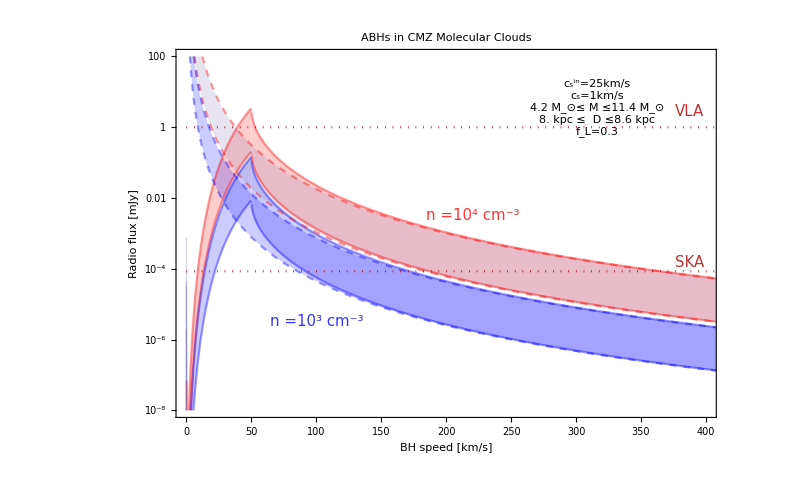

```mathematica
Legended[
LogPlot[
{
RFlux[v, 10^4,Mmin, Dmax], RFlux[v, 10^4,Mmax, Dmin], 
RFlux[v, 10^3,Mmin, Dmax], RFlux[v, 10^3,Mmax, Dmin],
RFluxBondi[v, 10^4,Mmin, Dmax], RFluxBondi[v, 10^4,Mmax, Dmin], 
RFluxBondi[v, 10^3,Mmin, Dmax], RFluxBondi[v, 10^3,Mmax, Dmin],
VLAsensitivity, SKAsensitivity},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-8, 10^2}},
FrameLabel->{labelv,labelRadioflux}, 
PlotLabel->CMZTitle,
ImageSize->800, 
PlotStyle->Join[
Table[{MyColors[[1]], Opacity[.4]}, {i,2}],Table[{MyColors[[2]], Opacity[.4]}, {i,2}], 
Table[{MyColors[[1]], Opacity[.4], Dashed}, {i,2}],Table[{MyColors[[2]], Opacity[.4], Dashed}, {i,2}], 
Table[{Directive [Darker[Red], Dotted]}, {i,2}]], 
Filling->Table[2*i-1->{2*i}, {i,4}],
FrameTicks->{{ticksF, None},{ticksv, None}}
],
{Placed[VLAText,{.95,.83}],
Placed[SKAText,{.95,.42}],

Placed[DisplayForm[StyleBox[ntext[4], MyColors[[1]], Opacity[.8], FontSize->20]],{.55,.55}],
Placed[DisplayForm[StyleBox[ntext[3], MyColors[[2]], Opacity[.8]]],{.26,.26}],
Placed[Framed[Column[{csintext[25],cstext[1], Mtext2[Mmin/Msun, Mmax/Msun],dtext2[Dmin/kpc, Dmax/kpc], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.78, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.78,.15}]}
]
```

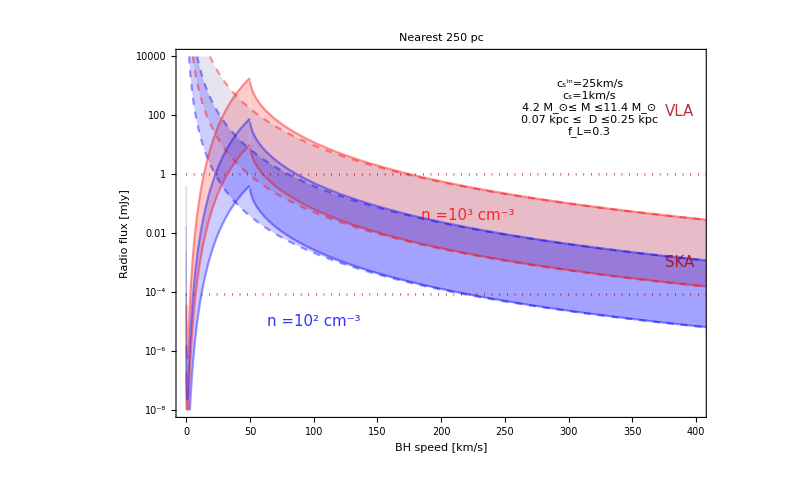

```mathematica
Legended[
LogPlot[
{
RFlux[v, 10^3,Mmin, DFmax], RFlux[v, 10^3,Mmax, DFmin], 
RFlux[v, 10^2,Mmin, DFmax], RFlux[v, 10^2,Mmax, DFmin],
RFluxBondi[v, 10^3,Mmin, DFmax], RFluxBondi[v, 10^3,Mmax, DFmin], 
RFluxBondi[v, 10^2,Mmin, DFmax], RFluxBondi[v, 10^2,Mmax, DFmin],
VLAsensitivity, SKAsensitivity},
{v,0,420}, 
Frame->True,
PlotRange->{{0,400},{10^-8, 10^4}},
FrameLabel->{labelv,labelRadioflux}, 
PlotLabel->NearTitle,
ImageSize->800, 
PlotStyle->Join[
Table[{MyColors[[1]], Opacity[.4]}, {i,2}],Table[{MyColors[[2]], Opacity[.4]}, {i,2}], 
Table[{MyColors[[1]], Opacity[.4], Dashed}, {i,2}],Table[{MyColors[[2]], Opacity[.4], Dashed}, {i,2}], 
Table[{Directive [Darker[Red], Dotted]}, {i,2}]], 
Filling->Table[2*i-1->{2*i}, {i,4}],
FrameTicks->{{ticksF, None},{ticksv, None}}
],
{Placed[VLAText,{.95,.83}],
Placed[SKAText,{.95,.42}],

Placed[DisplayForm[StyleBox[ntext[3], MyColors[[1]], Opacity[.8], FontSize->20]],{.55,.55}],
Placed[DisplayForm[StyleBox[ntext[2], MyColors[[2]], Opacity[.8]]],{.26,.26}],
Placed[Framed[Column[{csintext[25],cstext[1], Mtext2[Mmin/Msun, Mmax/Msun],dtext2[DFmin/kpc, DFmax/kpc], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.78, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi1 }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.78,.15}]}
]
```

## Invert Flux expression for M, v

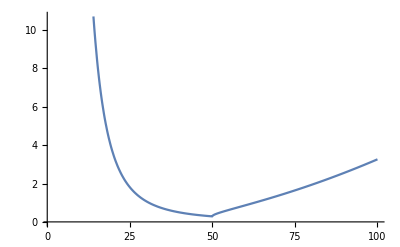

```mathematica
MSolution=Function[{v, n, d,cs, csin, t},NSolve[Flux[v,n,x2* Msun, d, cs, csin]/(erg/cm^2)== t && x2>0 , x2, Reals]];
MinMass= Function[{v, n, d, cs, csin, t},x2/.MSolution[v, n, d, cs, csin,t]];

Plot[MinMass[v, 10^3, .1*kpc,1, 25, Nustarsensitivity], {v, 1, 100}]
```

```mathematica
Do the same for the velocity:
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
VSolution=Function[{ n, m, d,cs, csin, t},NSolve[Flux[x3, n,m, d, cs, csin]/(erg/cm^2)== t && x3>0 , x3, Reals]];
MinVel= Function[{ n, m,  d, cs, csin, t},x3/.VSolution[ n,m, d, cs, csin,t][[1]]];
MaxVel= Function[{ n, m,  d, cs, csin, t},x3/.VSolution[ n,m, d, cs, csin,t][[2]]];
MinVel[ 10^3, 10*Msun,.1 kpc, 1, 25, Nustarsensitivity]
MaxVel[ 10^3, 10*Msun,.1 kpc, 1, 25, Nustarsensitivity]
(*Plot[{MinVel[10^3, m*Msun, .1*kpc,1, 25, Nustarsensitivity],MaxVel[10^3, m*Msun, .1*kpc,1, 25, Nustarsensitivity]}, {m, 1, 100}]*)
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

14.2965

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

168.445

```mathematica
VSolution[ 10^3, 10*Msun,.1 kpc, 1, 25, Nustarsensitivity][[2]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{x3→168.445}

### Plots!

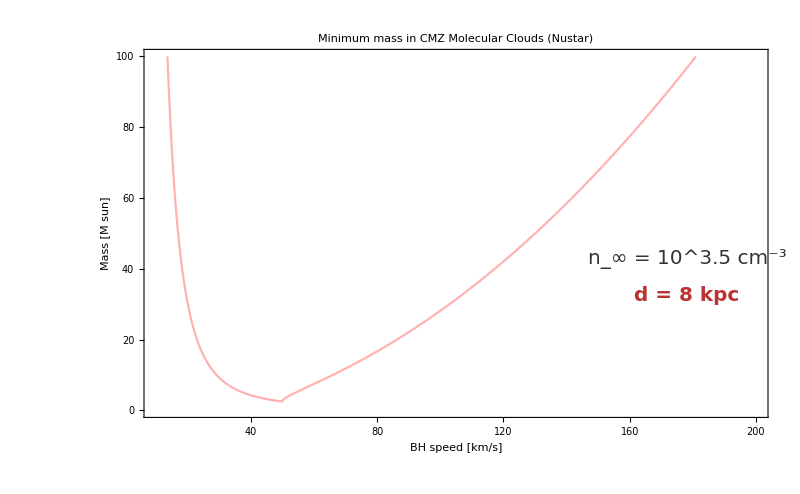

```mathematica
Legended[
Plot[
MinMass[v, 10^3.5, 8*kpc,1, 25, Nustarsensitivity], 
{v,10,200}, 
Frame->True,
PlotRange->{{10,200},{0,100}},
FrameLabel->{labelv,labelm}, 
PlotLabel->MinMassCMZTitle,
ImageSize->800, 
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,4}], {Darker[Red], Opacity[.6]}], 
FrameTicks->{{ticksF2, None},{ticksv2, None}}
],

{Placed[RhoText1,{.87,.43}], Placed[DText,{.87,.33}]}

]
```

## Define the PDFs

```mathematica
PofM[x_, mu_:mumass, sigma_:sigmamass]:=PDF[NormalDistribution[mu,sigma],x]
```

### Velocity

```mathematica
Pofv[x_, muv_:muvel]:=PDF[MaxwellDistribution[muv/Sqrt[8/Pi]],x]
```

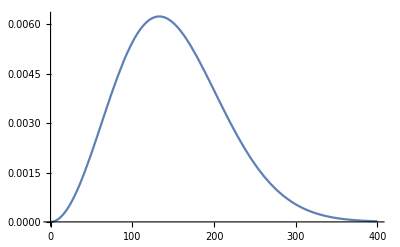

```mathematica
Plot[Pofv[v], {v,0,400}]
```

```mathematica
NIntegrate[Pofv[x, 130], {x, 35,60}]
```

0.0705669

```mathematica
Pofr[r_, rmin_:0.07, rmax_:0.25]:= 3/(rmax^3-rmin^3)*r^2
```

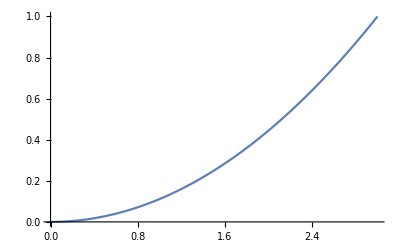

```mathematica
Plot[Pofr[r, 0, 3], {r, 0, 3}]
```

```mathematica
Integrate[Pofr[r, 0, 250], {r,0,250}]
```

1

## Define the integrals

### CMZ

```mathematica
fclouds[nc_]:=nCMZavg/nc
```

( below N= number of BHs in the CMZ)

```mathematica
NSourcesCMZBondi= Function[{N, mu, lambda, nclouds}, N*fclouds[ nclouds]*rwindow*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[FxBondi[v, nclouds, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> Nustarsensitivity], {v, 1, 400}, {m, 1,20}, AccuracyGoal->10] ];
```

```mathematica
NSourcesCMZRicotti= 
Function[{N, mu, lambda, csin,nclouds, k}, N*fclouds[ nclouds]*rwindow*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[Flux[v, nclouds, m*Msun, 8.3*kpc, csCMZ, csin, k]/(erg/cm^2)> Nustarsensitivity], {v, 1, 400}, {m, 1,20}, AccuracyGoal->10] ];
```

```mathematica
NSourcesRadioCMZRicottiSKA= Function[{N, mu, lambda, csin,nclouds,k}, N*fclouds[nclouds]*rwindow*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v,nclouds, m*Msun, 8.3*kpc, csCMZ, csin, k]> SKAsensitivity], {v, 1, 400}, {m, 1,20}, AccuracyGoal->10] ];

NSourcesRadioCMZRicottiVLA= Function[{N, mu, lambda, csin,nclouds, k}, N*fclouds[nclouds]*rwindow*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, nclouds, m*Msun, 8.3*kpc, csCMZ, csin, k]> VLAsensitivity], {v, 1, 400}, {m, 1,20}, AccuracyGoal->10] ];
```

### Fender Setup

Bondi scenario. Fender finds max lambda=0.01 for the no kick scenario. For this lambda no sources in the high kick scenario.

```mathematica
NSourcesNearBondi= Function[{lambda, mu},NcloudsNear1*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[FxBondi[v, 10^3, m*Msun, r*kpc, cs1Fender]/(erg/cm^2)> FendersensitivityX], {v, 1, 400}, {m, 1,100}, {r, 0.07, 0.250}, AccuracyGoal->10] +
NcloudsNear2*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[FxBondi[v, 10^2, m*Msun, r*kpc, cs2Fender]/(erg/cm^2)> FendersensitivityX], {v, 1, 400}, {m, 1,100}, {r, 0.07, 0.250}, AccuracyGoal->10]];
```

```mathematica
NSourcesNearRicotti= Function[{lambda, mu, csin},NcloudsNear1*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[Flux[v, 10^3, m*Msun, r*kpc, cs1Fender, csin]/(erg/cm^2)> FendersensitivityX], {v, 0, Infinity}, {m, 0,Infinity}, {r, 0.07, 0.250}, AccuracyGoal->10] +
NcloudsNear2*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[Flux[v, 10^2, m*Msun, r*kpc, cs2Fender, csin]/(erg/cm^2)> FendersensitivityX], {v, 0, Infinity}, {m, 0,Infinity}, {r, 0.07, 0.250}, AccuracyGoal->10]];
```

```mathematica
NRadioSourcesNearBondiVLA= Function[{lambda, mu},NcloudsNear1*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[RFluxBondi[v, 10^3, m*Msun, r*kpc, cs1Fender]/(erg/cm^2)> VLAsensitivity], {v, 1, 400}, {m, 1,100}, {r, 0.07, 0.250}, AccuracyGoal->10] +
NcloudsNear2*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[RFluxBondi[v, 10^2, m*Msun, r*kpc, cs2Fender]/(erg/cm^2)> VLAsensitivity], {v, 1, 400}, {m, 1,100}, {r, 0.07, 0.250}, AccuracyGoal->10]];
```

```mathematica
NRadioSourcesNearRicottiVLA= Function[{lambda, mu, csin},NcloudsNear1*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[RFlux[v, 10^3, m*Msun, r*kpc, cs1Fender, csin]/(erg/cm^2)> VLAsensitivity], {v, 0, Infinity}, {m, 0,Infinity}, {r, 0.07, 0.250}, AccuracyGoal->10] +
NcloudsNear2*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Pofr[r]*Boole[RFlux[v, 10^2, m*Msun, r*kpc, cs2Fender, csin]/(erg/cm^2)> VLAsensitivity], {v, 0, Infinity}, {m, 0,Infinity}, {r, 0.07, 0.250}, AccuracyGoal->10]];
```

## Plot the expected value for N Xray (Nustar)

### Local Region (Fender)

```mathematica
Legended[
Plot[{  
NSourcesNearRicotti[1, muNoKickFender, 25], 
NSourcesNearRicotti[1, muHighKickFender,25],
NSourcesNearBondi[lambda, muNoKickFender], 
NSourcesNearBondi[lambda, muHighKickFender],
100},
 {lambda, 10^-3, 1},
PlotPoints->2,   
MaxRecursion->0,
Frame->True,
PlotLabel->NearTitle,
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;2]],Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[1;;2]],
{Directive [Darker[Red], Dashed]}], 
FrameLabel->{labelLambda,labelN}, 
FrameTicks->{{ticksN2, None},{ticksLambda, None}},
ImageSize->800,
PlotLabels->{labelBondiNo,labelBondiHigh, labelRicottiNo,labelRicottiHigh, None}, 
PlotStyle->{Automatic, Automatic, Thick, Thick, Dashed}, 
PlotLabel->"Nuber of X-ray Sources",
PlotRange->{{0,1}, {0,200}
} 
],
{Placed[FenderText,{.9,.53}],

Placed[DisplayForm[StyleBox["No kick", MyColors[[1]], Opacity[.6], FontSize->15]],{.1,.16}],
Placed[DisplayForm[StyleBox["High kick", MyColors[[2]], Opacity[.6], FontSize->15]],{.35,.16}],
Placed[Framed[Column[{csintext[25],cstext[1], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.25}]}
]
```

Callout::copos: {Bottom {Automatic,Automatic}[{3.12478,210.}],Automatic} is not a valid position for the placement of callouts.

Callout::copos: {Bottom {Automatic,Automatic}[{6.69442,210.}],Automatic} is not a valid position for the placement of callouts.

Callout::copos: {Bottom {Automatic,Automatic}[{0.570268,210.}],Automatic} is not a valid position for the placement of callouts.

General::stop: Further output of Callout::copos will be suppressed during this calculation.

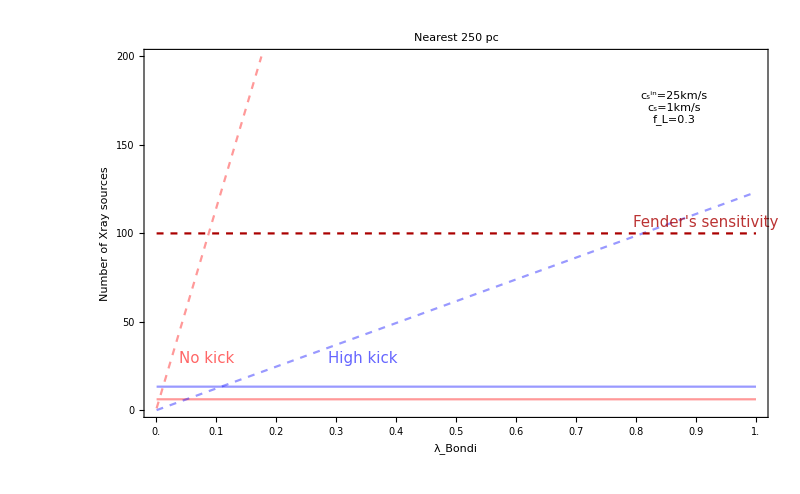

Velocity dependence in the two descriptions

```mathematica
Plot[{
NSourcesNearRicotti[1, mu, 25],
NSourcesNearBondi[1, mu],
NSourcesNearBondi[0.01, mu],

100},
 {mu, 5, 200},
PlotPoints->5,   (*increase this for better resolution*)
(*MaxRecursion->0,*)
Frame->True,
PlotLabel->NearTitle,
PlotStyle->Join[{Directive[MyColors[[1]], Opacity[.4]]},Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[2;;3]],
{Directive [Darker[Red], Dotted]}], 
FrameLabel->{labelavv,labelN}, 
FrameTicks->{{ticksN2, None},{ticksv, None}},
ImageSize->800, 
PlotStyle->{Automatic, Automatic, Thick, Dashed}, 
PlotLabel->"Nuber of X-ray Sources",
PlotRange->{{0,200}, {0,200}},
Epilog -> {
Text[FenderText,{.9,.53}],
Text[DisplayForm[StyleBox[RowBox[{SubscriptBox["λ", "Bondi"], "= 1"}] , MyColors[[2]], Opacity[.6], FontSize->15]],{90,180}],
Text[DisplayForm[StyleBox[RowBox[{SubscriptBox["λ", "Bondi"], "= 0.01"}], MyColors[[3]], Opacity[.6], FontSize->15]],{20,30}],
Text[Framed[Column[{csintext[25],cstext[1], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {180, 170}],
Text[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{180,50}],
{  Gray ,Thickness[.01], Arrow[{{muNoKickFender,40},{muNoKickFender,10}}]},
{  Gray,Thickness[.01], Arrow[{{muHighKickFender,40},{muHighKickFender,10}}]}

}
]
```

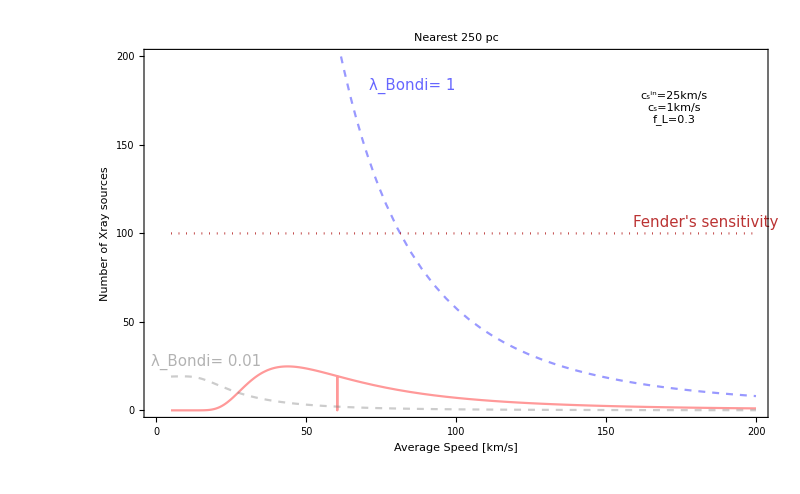

### Central Molecular Zone

Callout::copos: {Bottom {Automatic,Automatic}[{0.0775667,460.303}],Automatic} is not a valid position for the placement of callouts.

Callout::copos: {Bottom {Automatic,Automatic}[{0.122991,376.204}],Automatic} is not a valid position for the placement of callouts.

Callout::copos: {Bottom {Automatic,Automatic}[{179.145,376.204}],Automatic} is not a valid position for the placement of callouts.

General::stop: Further output of Callout::copos will be suppressed during this calculation.

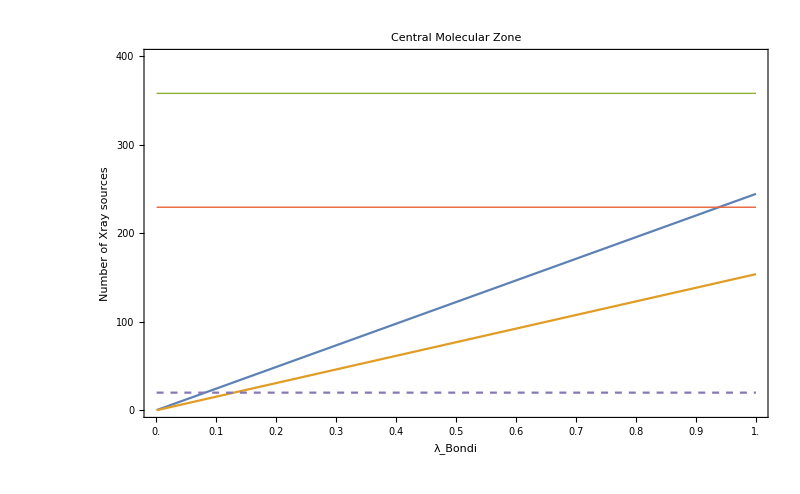

```mathematica
Legended[
Plot[{NSourcesCMZBondi[NCMZ, mulowCMZ, lambda, 10^3.5], 
NSourcesCMZBondi[NCMZ,  muhighCMZ, lambda, 10^3.5], 
NSourcesCMZRicotti[NCMZ, mulowCMZ, 1, 25, 10^3.5, 0.3], 
NSourcesCMZRicotti[NCMZ, muhighCMZ, 1, 25, 10^3.5, 0.3],
20},
 {lambda, 10^-3, 1},
PlotPoints->2,   (*increase this for better resolution*)
MaxRecursion->0,
Frame->True,
PlotLabel->CMZtitle,
FrameLabel->{labelLambda,labelN}, 
FrameTicks->{{ticksN, None},{ticksLambda, None}},
ImageSize->800,
PlotLabels->{labelBondiLow,labelBondiHigh, labelRicottiLow,labelRicottiHigh, labelNustarsensitivity}, 
PlotStyle->{Automatic, Automatic, Thick, Thick, Dashed}, 
PlotLabel->"Nuber of X-ray Sources",
PlotRange->{{0,1}, {0,400}
} 
],
None
]
```

```mathematica
Legended[
LogPlot[{NSourcesCMZRicotti[NCMZ, mu, 1, 25, 10^3.5, 0.3],
NSourcesCMZRicotti[NCMZ, mu, 1, 10, 10^3.5, 0.3],
NSourcesCMZBondi[NCMZ, mu, 1, 10^3.5],
NSourcesCMZBondi[NCMZ, mu, 0.01, 10^3.5],
70},
 {mu, 5, 400},
PlotPoints->50,   (*increase this for better resolution*)
(*MaxRecursion->0,*)
Frame->True,
PlotLabel->CMZtitle,
FrameLabel->{labelavv,labelN}, 
FrameTicks->{{ticksNlog, None},{ticksv, None}},
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;2]],Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[3;;4]],
{Directive [Darker[Red], Dotted]}], 
ImageSize->800,
PlotStyle->{Automatic, Automatic, Thick, Dashed},
PlotRange->{{0,400}, {1,10^4}} 
],
{Placed[NustarText,{.9,.5}],
Placed[DisplayForm[StyleBox[csintext[25], MyColors[[1]], Opacity[.6], FontSize->15]],{.58,.6}],
Placed[DisplayForm[StyleBox[csintext[10], MyColors[[2]], Opacity[.6], FontSize->15]],{.48,.4}],
Placed[DisplayForm[StyleBox[RowBox[{SubscriptBox["λ", "Bondi"], "= 1"}] , MyColors[[3]], Opacity[.6], FontSize->15]],{.14,.94}],
Placed[DisplayForm[StyleBox[RowBox[{SubscriptBox["λ", "Bondi"], "= 0.01"}], MyColors[[4]], Opacity[.6], FontSize->15]],{.20,.39}],
Placed[Framed[Column[{cstext[1], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.15}]}
]
```

$Aborted

### CMZ, as a function of the luminosity fraction in Xrays

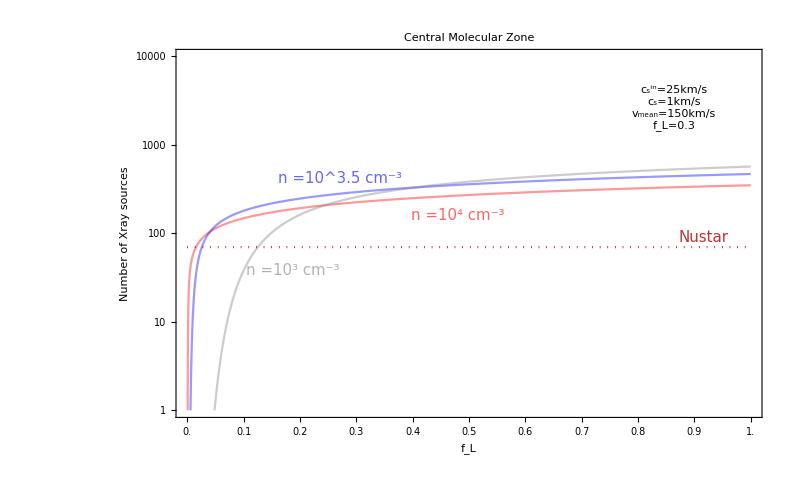

```mathematica
Legended[
LogPlot[{
NSourcesCMZRicotti[NCMZ, 150, 1, 25, 10^4, k],
NSourcesCMZRicotti[NCMZ, 150, 1, 25, 10^3.5, k],
NSourcesCMZRicotti[NCMZ, 150, 1, 25, 10^3, k],
70

},
{k, 0, 1},
PlotPoints->50,   (*increase this for better resolution*)
(*MaxRecursion->0,*)
PlotLabel->CMZtitle, 
Frame->True,
FrameLabel->{labelfl,labelN}, 
FrameTicks->{{ticksNlog, None},{ticksLambda, None}},
ImageSize->800,
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;3]],
{Directive [Darker[Red], Dotted]}],
PlotRange->{{0,1}, {1,10^4}} 
],
{Placed[NustarText,{.9,.49}],
Placed[DisplayForm[StyleBox[ntext[4], MyColors[[1]], Opacity[.6], FontSize->15]],{.48,.55}],
Placed[DisplayForm[StyleBox[ntext[3.5], MyColors[[2]], Opacity[.6], FontSize->15]],{.28,.65}],
Placed[DisplayForm[StyleBox[ntext[3], MyColors[[3]], Opacity[.6], FontSize->15]],{.2,.40}],
Placed[Framed[Column[{csintext[25],cstext[1], vtext[150],  fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}]
}
]
```

### As a function of cloud density

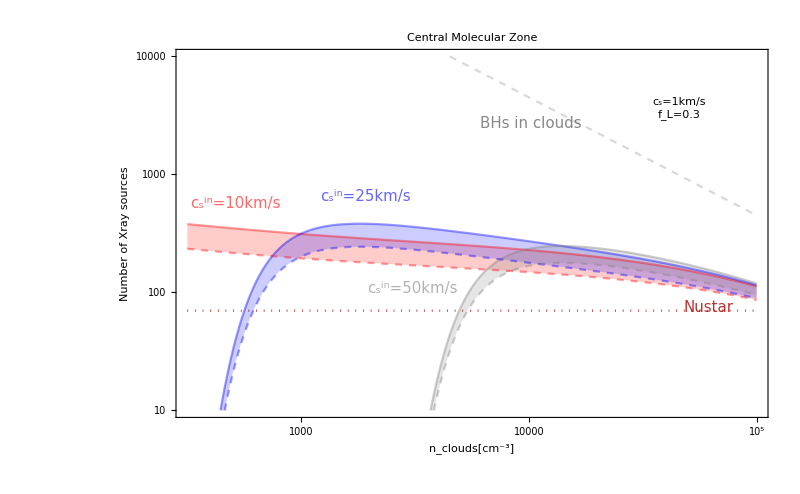

```mathematica
Legended[
LogLogPlot[
{NSourcesCMZRicotti[NCMZ, mulowCMZ, 1, 10, n, .3],
NSourcesCMZRicotti[NCMZ, mulowCMZ, 1, 25, n, .3],
NSourcesCMZRicotti[NCMZ, mulowCMZ, 1, 50, n, .3],
NSourcesCMZRicotti[NCMZ, muhighCMZ, 1, 10, n, .3],
NSourcesCMZRicotti[NCMZ, muhighCMZ, 1, 25, n, .3],
NSourcesCMZRicotti[NCMZ, muhighCMZ, 1, 50, n, .3],
NCMZ*fclouds[n],
70
},
{n, 10^2.5, 10^5},
PlotPoints->50,   (*increase this for better resolution*)
(*MaxRecursion->0,*)

Frame->True,
PlotLabel->CMZtitle, 
FrameLabel->{labelnclouds,labelN}, 
FrameTicks->{{ticksNlog, None},{ticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[Directive[color, Opacity[.4]], {color, MyColors}][[1;;3]],Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[1;;3]],
 {Directive [Gray, Opacity[.3], Dashed]}, {Directive [Darker[Red], Dotted]}], 
Filling->{1->{4}, 2->{5}, 3->{6}},
PlotRange->{{10^2.5,10^5}, {10, 10^4}} 
], 

{Placed[NustarText,{.9,.3}],
Placed [DisplayForm[StyleBox["BHs in clouds",FontSize->15, Darker[Gray], Opacity[.7]]], {.6,.8}],
Placed[DisplayForm[StyleBox[csintext[10], MyColors[[1]], Opacity[.6], FontSize->15]],{.1,.58}],
Placed[DisplayForm[StyleBox[csintext[25], MyColors[[2]], Opacity[.6], FontSize->15]],{.32,.60}],
Placed[DisplayForm[StyleBox[csintext[50], MyColors[[3]], Opacity[.6], FontSize->15]],{.4,.35}],
Placed[Framed[Column[{cstext[1],  fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelLow, labelHigh }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.15}]
}
]
```

## Plot the expected value for N radio (SKA)

### Nearest 250 pc

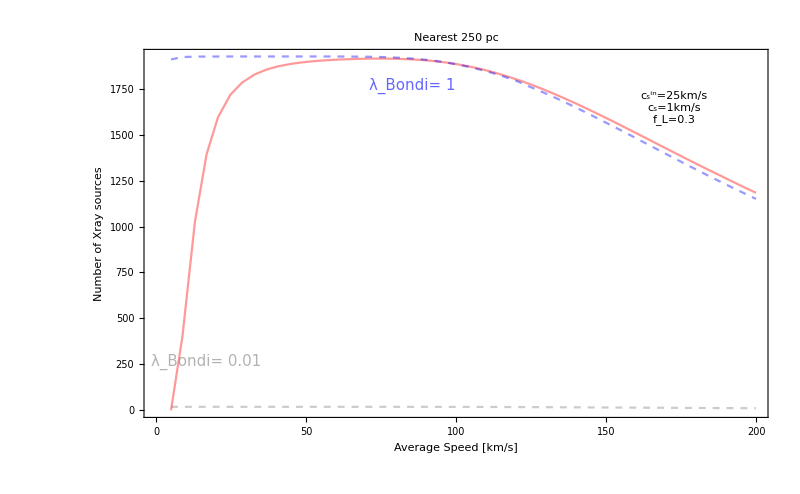

```mathematica
Legended[
Plot[{
NRadioSourcesNearRicottiVLA[1, mu, 25],
NRadioSourcesNearBondiVLA[1, mu],
NRadioSourcesNearBondiVLA[0.01, mu]},
 {mu, 5, 200},
PlotPoints->50,   (*increase this for better resolution*)
MaxRecursion->0,
Frame->True,
PlotLabel->NearTitle,
PlotStyle->Join[{Directive[MyColors[[1]], Opacity[.4]]},Table[Directive[color, Opacity[.4], Dashed], {color, MyColors}][[2;;3]],
{Directive [Darker[Red], Dotted]}], 
FrameLabel->{labelavv,labelN}, 
FrameTicks->{{Automatic, None},{ticksv, None}},
ImageSize->800, 
PlotStyle->{Automatic, Automatic, Thick, Dashed}, 
PlotLabel->"Nuber of X-ray Sources",
PlotRange->{Automatic, Automatic} 
],
{

Placed[DisplayForm[StyleBox[RowBox[{SubscriptBox["λ", "Bondi"], "= 1"}] , MyColors[[2]], Opacity[.6], FontSize->15]],{.43,.9}],
Placed[DisplayForm[StyleBox[RowBox[{SubscriptBox["λ", "Bondi"], "= 0.01"}], MyColors[[3]], Opacity[.6], FontSize->15]],{.1,.15}],
Placed[Framed[Column[{csintext[25],cstext[1], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {.85, .84}],
 Placed[Framed[LineLegend[{ Gray, {Gray, Dashed}},{labelRicotti, labelBondi }], Background->White,RoundingRadius->5, FrameStyle->Gray], 
{.85,.25}]}
]
```

### CMZ, as a function of cloud density

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.211688 and 0.0000217666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.14143 and 0.0000154683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.236984 and 0.0000261488 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

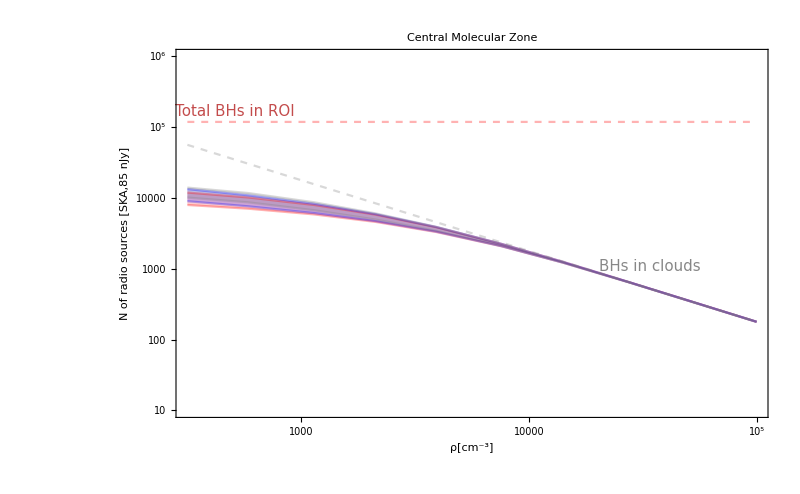

```mathematica
Legended[
LogLogPlot[
{NSourcesRadioCMZRicottiSKA[NCMZ, mulowCMZ, 1, 10, n, .3],
NSourcesRadioCMZRicottiSKA[NCMZ, muhighCMZ, 1, 10, n, .3],
NSourcesRadioCMZRicottiSKA[NCMZ,  mulowCMZ, 1, 25, n, .3],
NSourcesRadioCMZRicottiSKA[NCMZ, muhighCMZ, 1, 25, n, .3],
NSourcesRadioCMZRicottiSKA[NCMZ, mulowCMZ, 1, 50, n, .3],
NSourcesRadioCMZRicottiSKA[NCMZ, muhighCMZ, 1, 50, n, .3],
NwindowCMZ,
NwindowCMZ*fclouds[n]
},
{n, 10^2.5, 10^5},
PlotPoints->10,   (*increase this for better resolution*)
MaxRecursion->0,
MaxRecursion->0,
PlotPoints->10,
Frame->True,
PlotLabel->CMZtitle, 
FrameLabel->{labelrho,labelNRadio}, 
FrameTicks->{{ticksNlog, None},{ticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],Table[{Blue, Opacity[.3]}, {i,2}], Table[{Gray, Opacity[.3]}, {i,2}], {{Red, Opacity[.3], Dashed},{Gray, Opacity[.3], Dashed}}],
Filling->{1->{2}, 3->{4}, 5->{6}},
PlotRange->{{10^2.5,10^5}, {10, 10^6}} 
], 
{Placed [DisplayForm[StyleBox["Total BHs in ROI",FontSize->15, Darker[Red], Opacity[.7]]], {.1,.83}],
Placed [DisplayForm[StyleBox["BHs in clouds",FontSize->15, Darker[Gray], Opacity[.7]]], {.8,.41}],
 Placed[Framed[linelegendcs,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]}
]
```

## Nustar bound on the Number of BHs

Define a function to compute the bound on total number of BHs

```mathematica
NtotsolveRicotti=Function[{mu, csin, ncold, k},NSolve[NSourcesCMZRicotti[N.15*.02,mu,1, csin, ncold, k]== 70 && N>0 , N , Reals]];
NtotBoundNustarRicotti=Function[{mu, csin, ncold, k}, N/.NtotsolveRicotti[mu, csin, ncold, k]];
```

```mathematica
NtotsolveBondi=Function[{mu, lambda, ncold},NSolve[NSourcesCMZBondi[N.15*.02,mu,lambda, ncold]== 70 && N>0 , N , Reals]];
NtotBoundNustarBondi=Function[{mu, lambda, ncold}, N/.NtotsolveBondi[mu, lambda, ncold]];
```

Now define the same function but for the number of BH in the CMZ

Our naive estimate based on the literature is

```mathematica
NCMZ*fclouds[10^4]
```

4500

```mathematica
NwindowCMZ*fclouds[10^4]
```

1784.75

The following gives us the total number of BH in the CMZ that corresponds to the nustar bound.

```mathematica
NsolveRicotti=Function[{mu, csin, nclouds, k},NSolve[NSourcesCMZRicotti[N,mu,1, csin, nclouds, k]== 70 && N>0 , N , Reals]];
NBoundNustarRicotti=Function[{mu, csin, nclouds, k}, N/.NsolveRicotti[mu, csin, nclouds, k]];

NsolveBondi=Function[{mu, lambda, nclouds, k},NSolve[NSourcesCMZBondi[N,mu,lambda, nclouds, k]== 70 && N>0 , N , Reals]];
NBoundNustarBondi=Function[{mu, lambda, nclouds, k}, N/.NsolveBondi[mu, lambda, nclouds, k]];
```

To get the n of BHs in the CMZ clouds we must multiply by fclouds[nclouds]:

```mathematica
NCloudsBoundNustarRicotti =Function[{mu, lambda, nclouds, k},NBoundNustarRicotti[mu, lambda, nclouds, k]*fclouds[nclouds]];
NCloudsBoundNustarBondi  =Function[{mu, lambda, nclouds, k},NBoundNustarBondi[mu, lambda, nclouds, k]*fclouds[nclouds]];
```

```mathematica
NtotBoundNustarRicotti[150, 10, 10^3.5, 0.3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{1.62578×10^6}

```mathematica
NBoundNustarRicotti[150, 10, 10^3.5, 0.3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{4877.33}

```mathematica
NCloudsBoundNustarRicotti[150, 10, 10^3.5, 0.3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{231.352}

### Total BHs in the galaxy

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

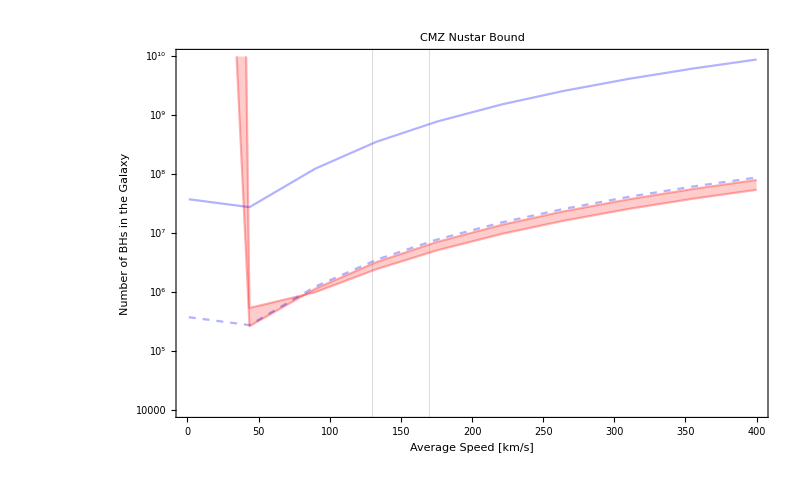

```mathematica
Legended[
Plot[
{NtotBoundNustarRicotti[mu, 10, 10^3.5, 0.3],
NtotBoundNustarRicotti[mu, 30, 10^3.5, 0.3],
NtotBoundNustarBondi[mu,0.01, 10^3.5],
NtotBoundNustarBondi[mu, 1, 10^3.5]
},
{mu, 1, 400},
PlotPoints->10,   (*increase this for better resolution*)
MaxRecursion->0,
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelavv,labelNtot}, 
FrameTicks->{{ticksNlog, None},{ticksv, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],{{Blue, Opacity[.3]}}, {{Blue, Opacity[.3], Dashed}}],
Filling->{1->{2}},
ScalingFunctions->{None,"Log"},
PlotRange->{{0,400}, {10^4, 10^10}} ,
GridLines->{{130, 170}, None}
], 

 Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]
]
```

### Bound on total number as a function of n_clouds

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

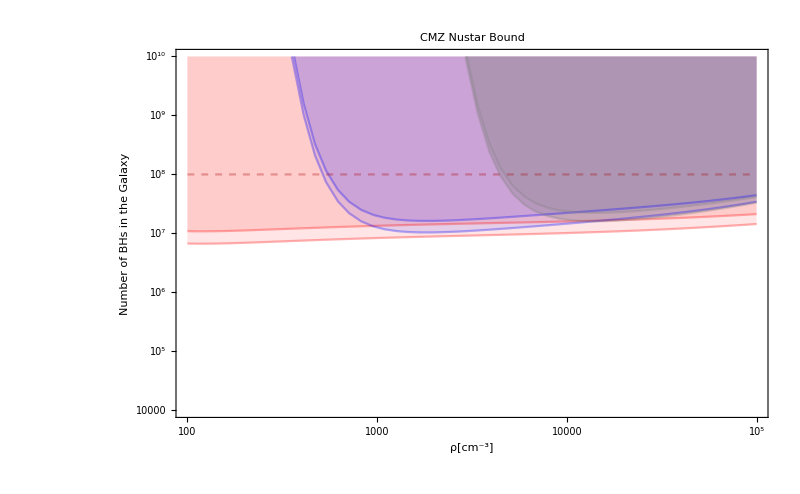

```mathematica
Legended[
LogLogPlot[
{NtotBoundNustarRicotti[mulowCMZ, 10, n, 0.3],
NtotBoundNustarRicotti[muhighCMZ, 10, n, 0.3],
NtotBoundNustarRicotti[mulowCMZ, 25, n, 0.3],
NtotBoundNustarRicotti[muhighCMZ, 25, n, 0.3],
NtotBoundNustarRicotti[mulowCMZ, 50, n, 0.3],
NtotBoundNustarRicotti[muhighCMZ, 50, n, 0.3],
10^8
},
{n, 10^2, 10^5},
PlotPoints->50,   (*increase this for better resolution*)
MaxRecursion->0,
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelrho,labelNtot}, 
FrameTicks->{{ticksNlog, None},{ticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],Table[{Blue, Opacity[.3]}, {i,2}], Table[{Gray, Opacity[.3]}, {i,2}], {{Darker[Red], Opacity[.3], Dashed}}],

Filling->{{2-> {Top,Directive[Red, Opacity[.2]]}},{1->{{2},Directive[Red, Opacity[.1]]}} ,
{4-> {Top,Directive[Blue, Opacity[.2]]}},{3->{{4},Directive[Blue, Opacity[.1]]}},
{6-> {Top,Directive[Gray, Opacity[.4]]}},{5->{{6},Directive[Gray, Opacity[.3]]}}},

PlotRange->{{10^2,10^5}, {10^4, 10^10}} 
], 

 Placed[Framed[linelegendcs,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]
]
```

### N of BHs in the CMZ clouds

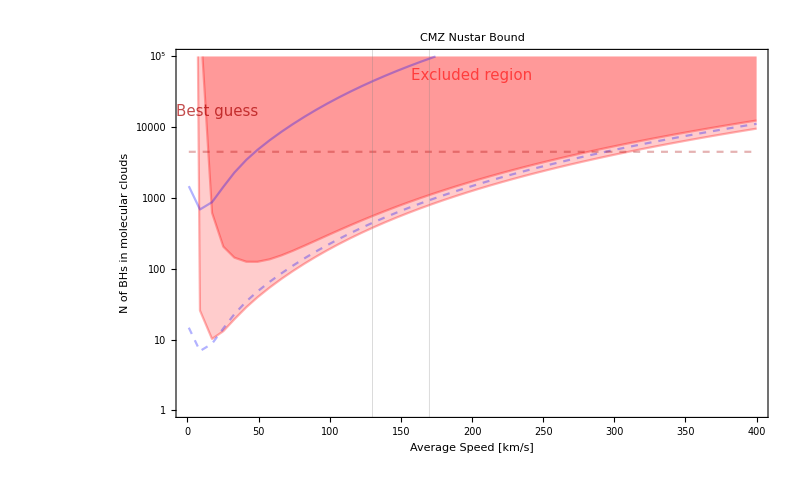

```mathematica
Legended[
Plot[
{NCloudsBoundNustarRicotti[mu, 10, 10^4, 0.3],
NCloudsBoundNustarRicotti[mu, 25,  10^4, 0.3],
NCloudsBoundNustarBondi[mu,0.01, 10^4, 0.3],
NCloudsBoundNustarBondi[mu,1, 10^4, 0.3],
NCMZ*fclouds[10^4]
},
{mu, 1, 400},
PlotPoints->50,   (*increase this for better resolution*)
MaxRecursion->0,
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelavv,labelNclouds}, 
FrameTicks->{{ticksNlog, None},{ticksv, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],{{Blue, Opacity[.3]}}, {{Blue, Opacity[.3], Dashed}}, {{Darker[Red], Opacity[.3], Dashed}}],
Filling->{{2-> {Top,Directive[Red, Opacity[.4]]}},{1->{{2},Directive[Red, Opacity[.2]]}} },
ScalingFunctions->{None,"Log"},
PlotRange->{{0,400}, {10^0, 10^5}} ,
GridLines->{{130, 170}, None}
], 

 {Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.35}],
Placed [DisplayForm[StyleBox["Best guess",FontSize->15, Darker[Red], Opacity[.7]]], {.07,.83}],
Placed [DisplayForm[StyleBox["Excluded region",FontSize->15, Red, Opacity[.6]]], {.5,.93}]}
]
```

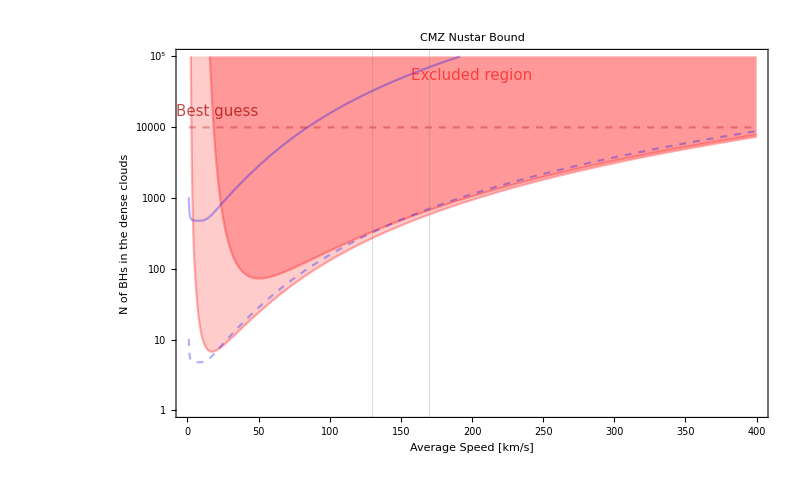

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

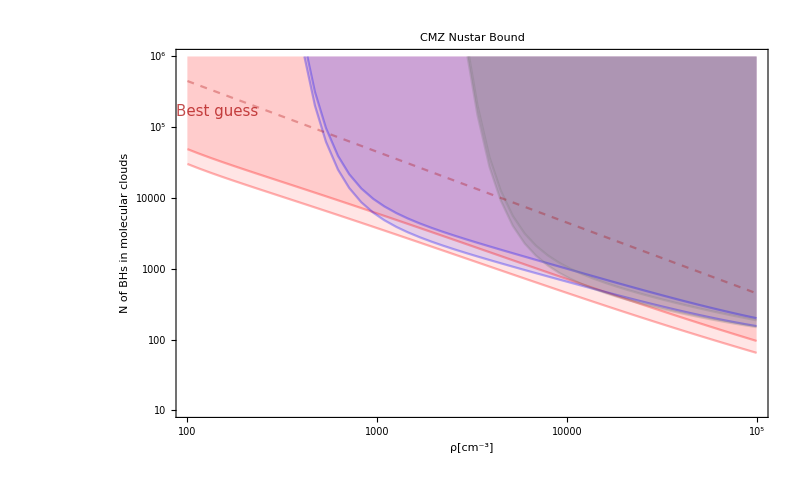

```mathematica
Legended[
LogLogPlot[
{NCloudsBoundNustarRicotti[mulowCMZ, 10, n,0.3],
NCloudsBoundNustarRicotti[muhighCMZ, 10, n, 0.3],
NCloudsBoundNustarRicotti[mulowCMZ, 25, n, 0.3],
NCloudsBoundNustarRicotti[muhighCMZ, 25, n, 0.3],
NCloudsBoundNustarRicotti[mulowCMZ, 50, n,0.3],
NCloudsBoundNustarRicotti[muhighCMZ, 50, n, 0.3],
NCMZ*fclouds[n]
},
{n, 10^2, 10^5},
PlotPoints->50,   (*increase this for better resolution*)
MaxRecursion->0,
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelrho,labelNclouds}, 
FrameTicks->{{ticksNlog, None},{ticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Red, Opacity[.3]}, {i,2}],Table[{Blue, Opacity[.3]}, {i,2}], Table[{Gray, Opacity[.3]}, {i,2}], {{Darker[Red], Opacity[.3], Dashed}}],

Filling->{{2-> {Top,Directive[Red, Opacity[.2]]}},{1->{{2},Directive[Red, Opacity[.1]]}} ,
{4-> {Top,Directive[Blue, Opacity[.2]]}},{3->{{4},Directive[Blue, Opacity[.1]]}},
{6-> {Top,Directive[Gray, Opacity[.4]]}},{5->{{6},Directive[Gray, Opacity[.3]]}}},


PlotRange->{{10^2,10^5}, {10, 10^6}} 
], 

 {Placed[Framed[linelegend,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}],
Placed [DisplayForm[StyleBox["Best guess",FontSize->15, Darker[Red], Opacity[.7]]], {.07,.83}]}
]
```

### Dependence on the luminosity factor k

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

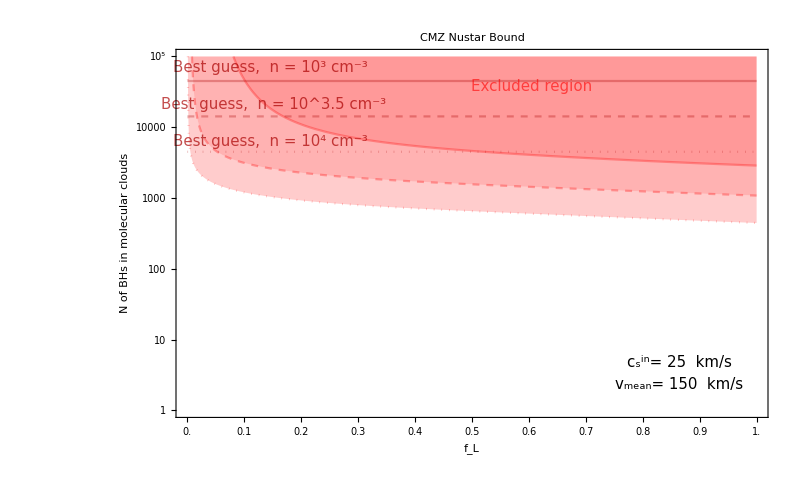

```mathematica
Legended[
Plot[
{NCloudsBoundNustarRicotti[150, 25, 10^4, k],
NCloudsBoundNustarRicotti[150, 25, 10^3.5, k],
NCloudsBoundNustarRicotti[150, 25,  10^3, k],

NCMZ*fclouds[10^4],
NCMZ*fclouds[ 10^3.5],
NCMZ*fclouds[10^3]
},
{k, 0, 1},
PlotPoints->50,   (*increase this for better resolution*)
Frame->True,
PlotLabel->CMZtitlecont, 
FrameLabel->{labelfl,labelNclouds}, 
FrameTicks->{{ticksNlog, None},{ticksLambda, None}},
ImageSize->800 ,
PlotStyle->{{Red, Opacity[.3], Dotted},{Red, Opacity[.3], Dashed}, {Red, Opacity[.3]}, {Darker[Red], Opacity[.3],  Dotted}, {Darker[Red], Opacity[.3], Dashed}, {Darker[Red], Opacity[.3]}},
Filling->{{3-> {Top,Directive[Red, Opacity[.4]]}},{1->{{2},Directive[Red, Opacity[.2]]}} , {2->{{3},Directive[Red, Opacity[.3]]}}},
ScalingFunctions->{None,"Log"},
PlotRange->{{0,1}, {10^0, 10^5}} 
], 


{Placed [DisplayForm[StyleBox[RowBox[{"Best guess, " "n = ", SuperscriptBox["10", "3"],SuperscriptBox["cm", "-3"]}],FontSize->15, Darker[Red], Opacity[.7]]], {.16,.95}],
Placed [DisplayForm[StyleBox[RowBox[{"Best guess, " "n = ", SuperscriptBox["10", "3.5"],SuperscriptBox["cm", "-3"]}],FontSize->15, Darker[Red], Opacity[.7]]], {.165,.85}],
Placed [DisplayForm[StyleBox[RowBox[{"Best guess, " "n = ", SuperscriptBox["10", "4"],SuperscriptBox["cm", "-3"]}],FontSize->15, Darker[Red], Opacity[.7]]], {.16,.75}],
Placed [DisplayForm[StyleBox["Excluded region",FontSize->15, Red, Opacity[.6]]], {.6,.90}],
Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 25  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 150  km/s"}],FontSize->15]],  {.85,.09}],
Placed[Framed[linelegendn,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.75}]}
]
```

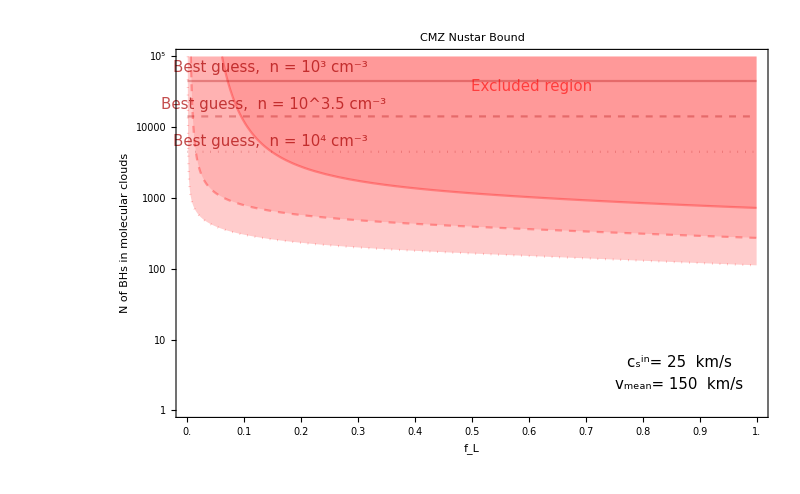

## Try different prescriptions for the gas density

### 1. Warm + cold clouds (Ferriere)

```mathematica
fwarm=0.3*150/10^2.5
fcold[nc_]:=0.7*150/nc
```

0.142302

```mathematica
NcloudsCMZ1=NCMZ*fcold[10^3.5]
NcloudsCMZ2=NCMZ*fwarm
```

9961.17

42690.7

```mathematica
NSourcesCMZBondi= Function[{N, mu, lambda, ncold}, N*fcold[ncold]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[FxBondi[v, ncold, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> Nustarsensitivity], {v, 1, 400}, {m, 1,100}] +
N*fwarm*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[FxBondi[v, 10^2.5, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> Nustarsensitivity], {v, 1, 400}, {m, 1,100}]];
```

```mathematica
NSourcesCMZRicotti= Function[{N, mu, lambda, csin,ncold, k}, N*fcold[ncold]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[Flux[v, ncold, m*Msun, 8.3*kpc, csCMZ, csin, k]/(erg/cm^2)> Nustarsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10] +
N*fwarm*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[Flux[v, 10^2.5, m*Msun, 8.3*kpc, csCMZ, csin, k]/(erg/cm^2)> Nustarsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10]];
```

```mathematica
NSourcesRadioCMZRicottiSKA2= Function[{N, mu, lambda, csin,ncold,nwarm, k}, N*fcold[ncold]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, ncold, m*Msun, 8.3*kpc, csCMZ, csin, k]> SKAsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->20] +
N*fwarm*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, nwarm, m*Msun, 8.3*kpc, csCMZ, csin, k]> SKAsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->20]];

NSourcesRadioCMZRicottiVLA2= Function[{N, mu, lambda, csin,ncold,nwarm, k}, N*fcold[ncold]*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, ncold, m*Msun, 8.3*kpc, csCMZ, csin, k]> VLAsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10] +
N*fwarm*lambda*NIntegrate[Pofv[v, mu]*PofM[m]*Boole[RFlux[v, nwarm, m*Msun, 8.3*kpc, csCMZ, csin, k]> VLAsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10]];
```

```mathematica
NSourcesRadioCMZRicottiSKA2[10^4, 100, 1, 25, 10^4,10^2.5, .3]
NSourcesRadioCMZRicottiVLA2[10^4, 100, 1, 25, 10^4,10^2.5, .3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.467815 and 0.0000384468 for the integral and error estimates.

770.501

0.

99% of BHs in dense molecular clouds would be detected by SKA:

```mathematica
NIntegrate[Pofv[v, 100]*PofM[m]*Boole[RFlux[v, 10^4, m*Msun, 8.3*kpc]> SKAsensitivity],{v, 1, 400}, {m, 1,100},  AccuracyGoal->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.99799

Also half of the BH in the warm clouds would emit above threshold:

```mathematica
NIntegrate[Pofv[v, 100]*PofM[m]*Boole[RFlux[v, 10^2.5, m*Msun, 8.3*kpc]> SKAsensitivity],{v, 1, 400}, {m, 1,100},  AccuracyGoal->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.467815 and 0.0000384468 for the integral and error estimates.

0.467815

These make up most of the visible sources since the filling factor is bigger:

```mathematica
10^4*fwarm
```

1423.02

```mathematica
10^4*fwarm*0.46
```

654.591

We must therefore take into account also the dependence on the density of these warm clouds.

```mathematica
10^4*fwarm*NIntegrate[Pofv[v, 100]*PofM[m]*Boole[RFlux[v, 10^3, m*Msun, 8.3*kpc]> SKAsensitivity],{v, 1, 400}, {m, 1,100},  AccuracyGoal->20] 
10^4*fwarm*NIntegrate[Pofv[v, 100]*PofM[m]*Boole[RFlux[v, 10^2, m*Msun, 8.3*kpc]> SKAsensitivity],{v, 1, 400}, {m, 1,100},  AccuracyGoal->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.777889 and 0.0000400218 for the integral and error estimates.

1106.95

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.227526 and 0.000022804 for the integral and error estimates.

323.775

### 2. Power law

## Plot the expected N for SKA in the allowed region

### With bound on total BHs in the Galaxy

```mathematica
NtotsolveRicottiRadio=Function[{mu, csin, ncold,nwarm, k, i},NSolve[NSourcesRadioCMZRicottiSKA[N.15*.02,mu,1, csin, ncold,nwarm, k]== i && N>0 , N , Reals]];
ContourNtotSKARicotti=Function[{mu, csin, ncold,nwarm, k, i}, N/.NtotsolveRicottiRadio[mu, csin, ncold,nwarm, k, i]];
```

```mathematica
NsolveRicottiRadio=Function[{mu, csin, nclouds, k, i},NSolve[NSourcesRadioCMZRicottiSKA[N,mu,1, csin, nclouds, k]== i && N>0 , N , Reals]];
ContourSKARicotti=Function[{mu, csin,nclouds, k, i}, N/.NsolveRicottiRadio[mu, csin, nclouds,k, i]];
ContourNCloudsSKARicotti  =Function[{mu, csin,nclouds, k, i},ContourSKARicotti[mu, csin,nclouds, k, i]*fclouds[nclouds]];
```

```mathematica
ContourNSKARicotti[150,25, 10^4,10^2.5, 0.3, 10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{50.4503}

```mathematica
contourlabels
```

{10^1,10^2,10^3,10^4,10^5}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.85421 and 0.0000319012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.85421 and 0.0000319012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.85421 and 0.0000319012 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

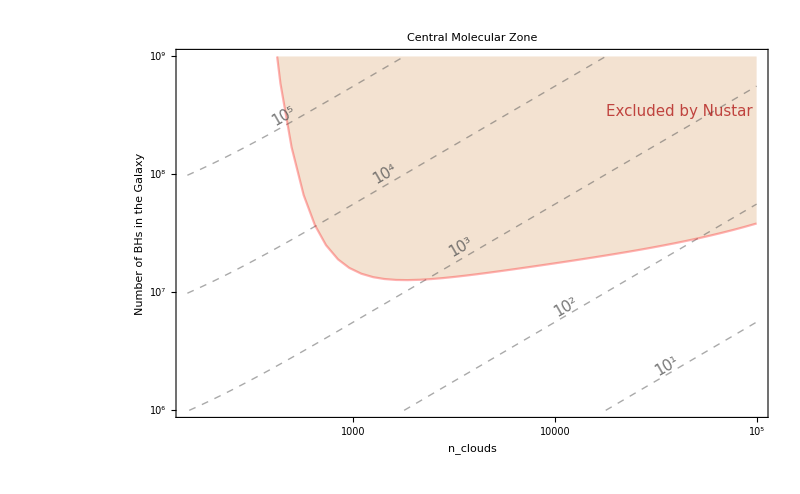

```mathematica
Legended[
LogLogPlot[
{
ContourNtotSKARicotti[150,25, n,10^2.5, 0.3, 10],
ContourNtotSKARicotti[150,25, n,10^2.5, 0.3, 10^2],
ContourNtotSKARicotti[150,25, n,10^2.5, 0.3, 10^3],
ContourNtotSKARicotti[150,25, n,10^2.5, 0.3, 10^4],
ContourNtotSKARicotti[150,25, n,10^2.5, 0.3, 10^5],
NtotBoundNustarRicotti[150, 25, n, 0.3]
},
{n, 150, 10^5},
PlotPoints->50,   (*increase this for better resolution*)
MaxRecursion->0,
Frame->True,
PlotLabel->CMZtitle, 
FrameLabel->{labelnclouds,labelNtot}, 
FrameTicks->{{ticksNlog, None},{ticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Darker[Gray], Opacity[.5], Dashed, Thick}, {i,5}], {{Red, Opacity[.3]}}],
Filling->{6->Top},

PlotLabels->Placed[contourlabels,Scaled[.5]],
PlotRange->{{150,10^5}, {10^6, 10^9}} 
],
{Placed [DisplayForm[StyleBox["Excluded by Nustar",FontSize->15, Darker[Red], Opacity[.7]]], {.85,.83}]}
]
```

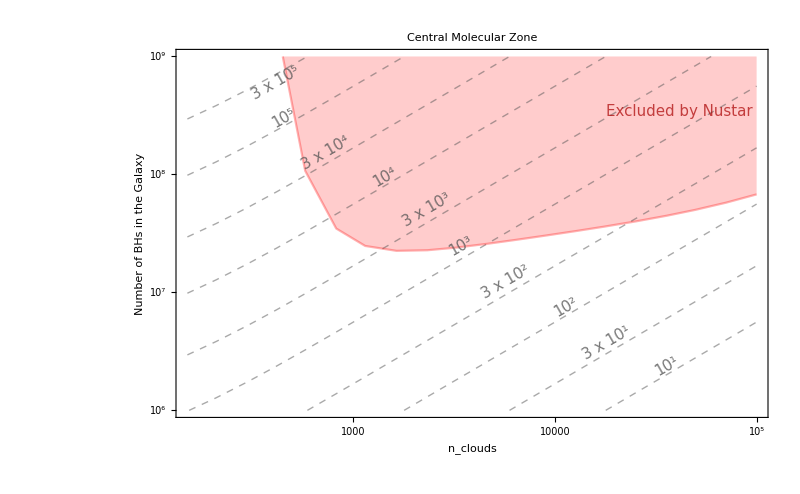

### Bound on BHs in the clouds

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.114231 and 0.000013146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.114231 and 0.000013146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.114231 and 0.000013146 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

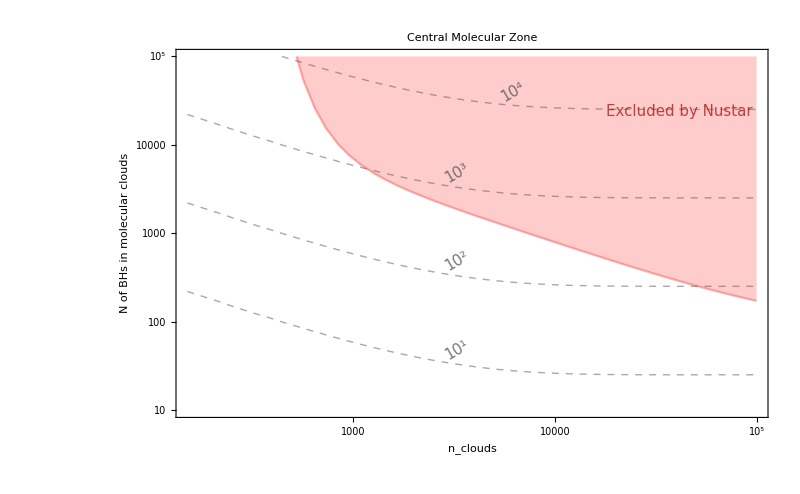

```mathematica
Legended[
LogLogPlot[
{
ContourNCloudsSKARicotti[150,25, n, 0.3, 10],
ContourNCloudsSKARicotti[150,25, n, 0.3, 10^2],
ContourNCloudsSKARicotti[150,25, n, 0.3, 10^3],
ContourNCloudsSKARicotti[150,25, n, 0.3, 10^4],
NCloudsBoundNustarRicotti[150, 25, n, .3]
},
{n, 150, 10^5},
PlotPoints->50,   (*increase this for better resolution*)
MaxRecursion->0,
Frame->True,
PlotLabel->CMZtitle, 
FrameLabel->{labelnclouds,labelNclouds}, 
FrameTicks->{{ticksNlog, None},{ticksrho, None}},
ImageSize->800 ,
PlotStyle->Join[Table[{Darker[Gray], Opacity[.5], Dashed, Thick}, {i,4}], {{Red, Opacity[.3]}}],
Filling->{5->Top},

PlotLabels->Placed[contourlabelsclouds,Scaled[.5]],
PlotRange->{{150,10^5}, {10^1, 10^5}} 
],
{Placed [DisplayForm[StyleBox["Excluded by Nustar",FontSize->15, Darker[Red], Opacity[.7]]], {.85,.83}]}
]
```

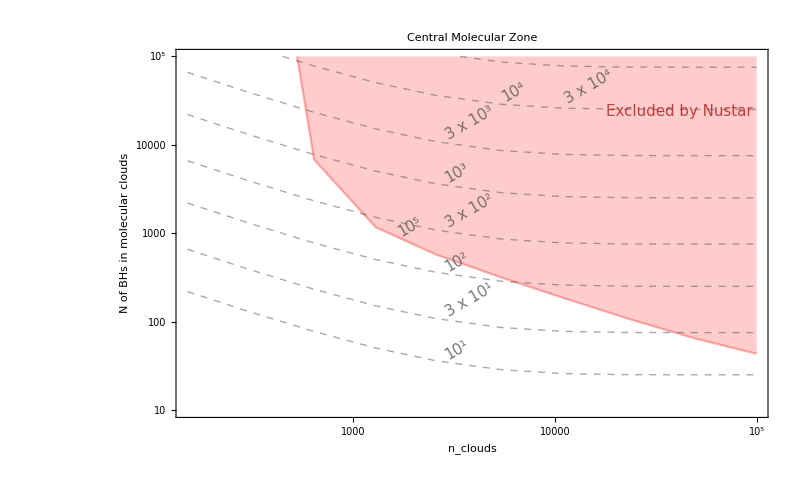

### Bound on lambda

## Apply the model to PBHs

```mathematica
Rs=16 kpc
Mbulge=0.4*1.84*10^10*Msun
Rbulge=2*kpc
rho0=Mbulge/(4*Pi*Rs^3*(Log[(Rs+Rbulge)/Rs]- Rbulge/(Rs+Rbulge)))
```

4.9376×10^20

1.46349×10^40

6.172×10^19

1.45004×10^-21

```mathematica
rhoNFW[r_]:=1/(r/Rs(1+r/Rs)^2)
```

```mathematica
Plot[rho0*rhoNFW[r], {r, 0, 10kpc}]
```

-Graphics-

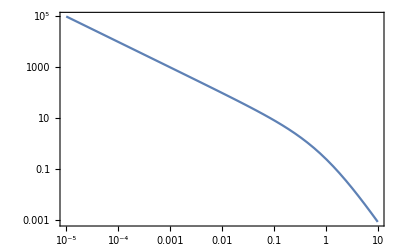

```mathematica
LogLogPlot[rhoNFW[r*Rs], {r, 10^-5,10^1}, Frame->True]
```

```mathematica
NIntegrate[rho0*rhoNFW[r]*r^2*4*Pi, {r, 0, Rbulge}]/Msun
```

7.36×10^9

```mathematica
DMMassCMZ=NIntegrate[rho0*2 Pi R*rhoNFW[Sqrt[R^2+z^2]], {R, 0, 0.16*kpc}, {z, -0.015*kpc, 0.015*kpc}]/Msun;
```

```mathematica
sigmamassPBH=10;
mumassPBH= 30;
```

```mathematica
NPBHCMZ=DMMassCMZ/mumassPBH
```

325660.

```mathematica
muvelPBH= Sqrt[8/Pi]*35
N[muvelPBH]
```

70 √(2/π)

55.8519

```mathematica
Clear[NPBHCMZRicotti1]
Clear[NsolveRicotti1PBH]
Clear[NBoundNustarRicotti1PBH]
```

### With gaussian mass function:

```mathematica
NPBHCMZBondi1= Function[{N, mu, lambda, nclouds}, N*fclouds[nclouds]*lambda*NIntegrate[Pofv[v, mu]*PofM[m, mumassPBH, sigmamassPBH ]*Boole[FxBondi[v, nclouds, m*Msun, 8.3*kpc, csCMZ]/(erg/cm^2)> Nustarsensitivity], {v, 1, 400}, {m, 1,100}]] ;
NPBHCMZRicotti1= Function[{N, mu, lambda, csin,nclouds, k, mumassPBH}, N*fclouds[nclouds]*lambda*NIntegrate[Pofv[v, mu]*PofM[m, mumassPBH, sigmamassPBH ]*Boole[Flux[v, nclouds, m*Msun, 8.3*kpc, csCMZ, csin,k]/(erg/cm^2)> Nustarsensitivity], {v, 1, 400}, {m, 1,100}, AccuracyGoal->10]] ;
```

```mathematica
NsolveRicotti1PBH=Function[{mu, csin, nclouds, k, mumassPBH},NSolve[NPBHCMZRicotti1[N,mu,1, csin,nclouds, k, mumassPBH]*rwindow== 10 && N>0 , N , Reals]];
NBoundNustarRicotti1PBH=Function[{mu, csin, nclouds, k, mumassPBH}, N/.NsolveRicotti1PBH[mu, csin, nclouds, k, mumassPBH]];

NsolveBondi1PBH=Function[{mu, lambda, nclouds},NSolve[NPBHCMZBondi1[N,mu,lambda, nclouds]*rwindow== 10 && N>0 , N , Reals]];
NBoundNustarBondi1PBH=Function[{mu, lambda, nclouds}, N/.NsolveBondi1PBH[mu, lambda,nclouds]];
```

```mathematica
ticksfDM=Table[Which[IntegerQ[Log[10,i]],{i,DisplayForm[StyleBox[SuperscriptBox["10",Log[10,i]],FontSize->20]],{.018,0},Black},
IntegerQ[Log[10,i]],{i,,{.018,0},Black},
True,{i,"",{.007,0},Black}],{i,Flatten[Table[10^j*k,{j,-5,0},{k,1,9}]]}];
labelfDM=DisplayForm[StyleBox[SubscriptBox["f", "DM"],FontSize->30]];
CMZtitlePBH=DisplayForm[StyleBox["CMZ Nustar Bound-PBH",FontSize->30]];
```

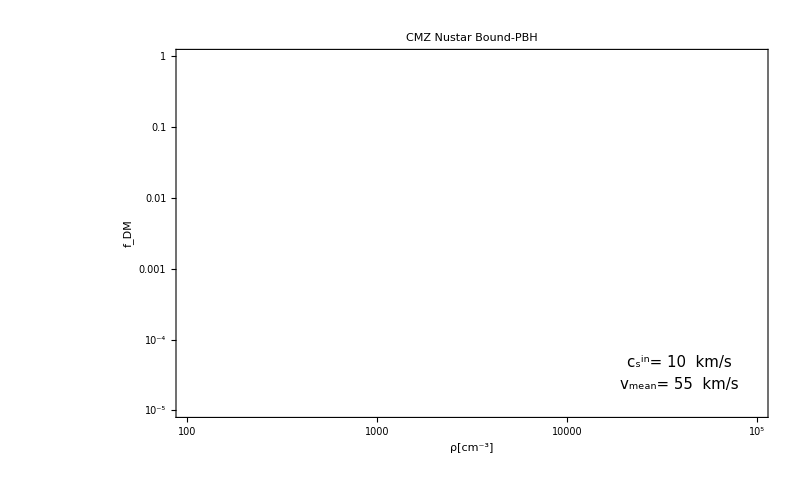

```mathematica
Legended[
LogLogPlot[
{NCloudsBoundNustarRicotti[muvelPBH, 10, n, 0.3, 30]/NPBHCMZ
},
{n, 10^2, 10^5},
Frame->True,
PlotLabel->CMZtitlePBH, 
FrameLabel->{labelrho,labelfDM}, 
FrameTicks->{{ticksfDM, None},{ticksrho, None}},
ImageSize->800 ,
PlotStyle->{Red, Opacity[.3]},

Filling->{2-> {Top,Directive[Red, Opacity[.2]]}},


PlotRange->{{10^2,10^5}, {10^-5, 1}}
], 

 {Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 10  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 55  km/s"}],FontSize->15]],  {.85,.09}]}
]
```

```mathematica
labelPBHM=DisplayForm[StyleBox[SubscriptBox["M", "PBH"],FontSize->30]];
```

```mathematica
ticksM= Table[If[IntegerQ[i/20],{i,DisplayForm[StyleBox[i,FontSize->20]],{.018,0},Black},{ i,"",{.007,0},Black}],{i,0,100,10}];
```

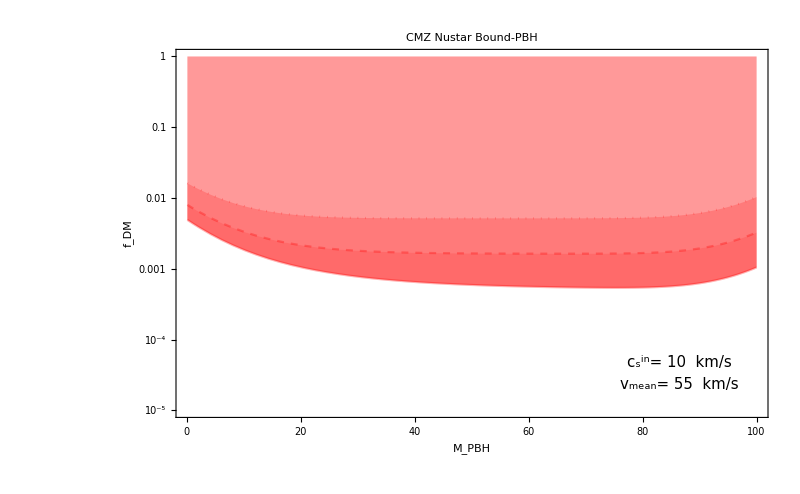

```mathematica
Legended[
LogPlot[
{NBoundNustarRicotti1PBH[muvelPBH, 10, 10^4, 0.3, m]/NPBHCMZ,
NBoundNustarRicotti1PBH[muvelPBH, 10, 10^3.5, 0.3, m]/NPBHCMZ,
NBoundNustarRicotti1PBH[muvelPBH, 10, 10^3, 0.3, m]/NPBHCMZ
},
{m, 0.1, 100},
Frame->True,
PlotLabel->CMZtitlePBH, 
FrameLabel->{labelPBHM,labelfDM}, 
FrameTicks->{{ticksfDM, None},{ticksM, None}},
ImageSize->800 ,
PlotStyle->{{Red, Opacity[.3], Dotted},{Red, Opacity[.3], Dashed}, {Red, Opacity[.3]}},

Filling->{{3-> {Top,Directive[Red, Opacity[.4]]}},{1->{{2},Directive[Red, Opacity[.2]]}} , {2->{{3},Directive[Red, Opacity[.3]]}}},


PlotRange->{{.1,100}, {10^-5, 1}}
], 

 {Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 10  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 55  km/s"}],FontSize->15]],  {.85,.09}],
Placed[Framed[linelegendn,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]}
]
```

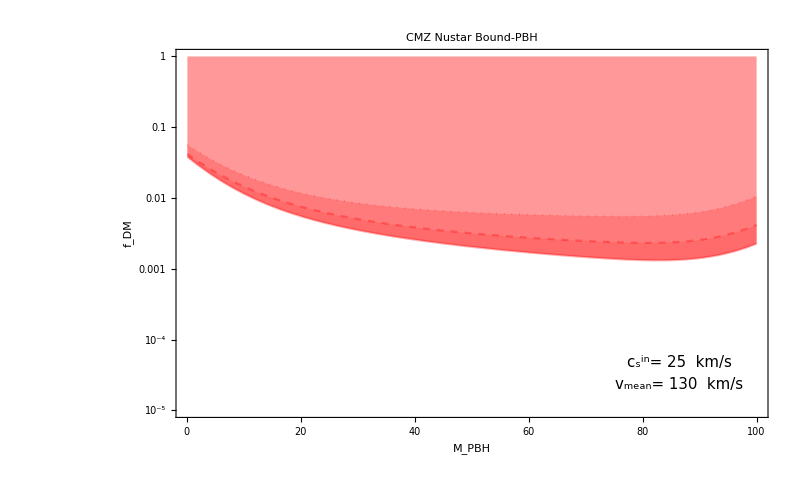

```mathematica
Legended[
LogPlot[
{NBoundNustarRicotti1PBH[130,25, 10^4, 0.3, m]/NPBHCMZ,
NBoundNustarRicotti1PBH[130,25, 10^3.5, 0.3, m]/NPBHCMZ,
NBoundNustarRicotti1PBH[130,25, 10^3, 0.3, m]/NPBHCMZ
},
{m, 0.1, 100},
Frame->True,
PlotLabel->CMZtitlePBH, 
FrameLabel->{labelPBHM,labelfDM}, 
FrameTicks->{{ticksfDM, None},{ticksM, None}},
ImageSize->800 ,
PlotStyle->{{Red, Opacity[.3], Dotted},{Red, Opacity[.3], Dashed}, {Red, Opacity[.3]}},

Filling->{{3-> {Top,Directive[Red, Opacity[.4]]}},{1->{{2},Directive[Red, Opacity[.2]]}} , {2->{{3},Directive[Red, Opacity[.3]]}}},


PlotRange->{{.1,100}, {10^-5, 1}}
], 

 {Placed [DisplayForm[StyleBox[RowBox[{ SuperscriptBox[SubscriptBox["c", "s"],"in" ],"= 25  km/s"}],FontSize->15]],  {.85,.15}],
Placed [DisplayForm[StyleBox[RowBox[{ SubscriptBox["v", "mean"] , "= 130  km/s"}],FontSize->15]],  {.85,.09}],
Placed[Framed[linelegendn,Background->White,RoundingRadius->5, FrameStyle->Gray], {.85,.85}]}
]
```

```mathematica
NBoundNustarRicotti1PBH[muvelPBH, 10, 10^4, 0.3, 30]
NBoundNustarRicotti1PBH[muvelPBH, 10, 10^4, 0.3, 1]
```

{1706.55}

{4809.42}

### With monochromatic mass function

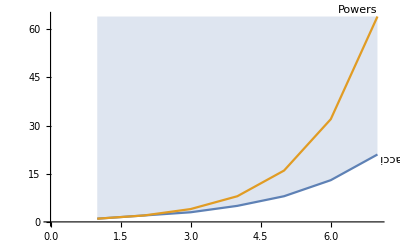

```mathematica
ListLinePlot[{{1,2,3,5,8,13,21},{1,2,4,8,16,32,64}},PlotRange->{Automatic, Automatic},Filling->{1->Top},PlotLabels->Placed[{Rotate["Fibonacci", Pi],"Powers"},Above]]
```

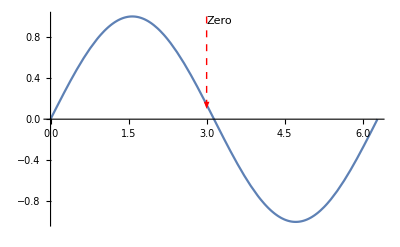

```mathematica
Plot[Sin[x],{x,0,2 Pi},Epilog->{{   Red, Dashed ,Arrow[{{3,1},{3,.1}}]},Text["Zero",{3 ,1},{-2,2}]}]
```

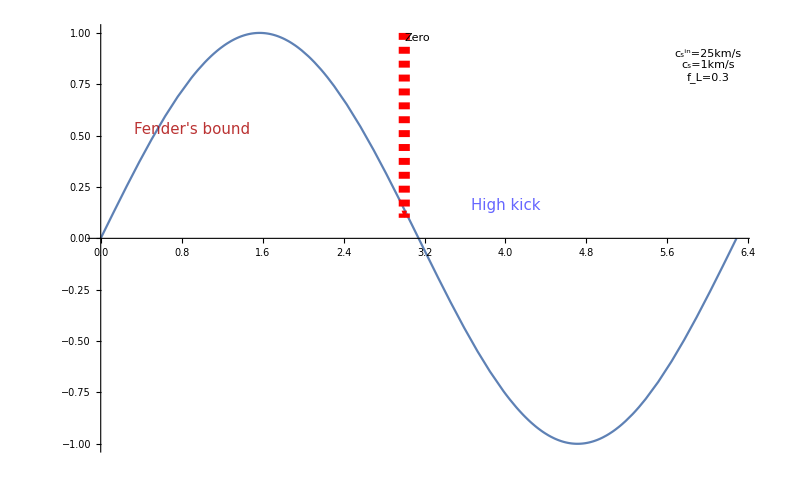

```mathematica
Plot[Sin[x],{x,0,2 Pi},ImageSize->800,
Epilog->{
{   Red, Dashed ,Thickness[.01], Arrow[{{3,1},{3,.1}}]},
Text["Zero",{3 ,1},{-2,2}],
Text[FenderText,{.9,.53}], 
Text[Framed[Column[{csintext[25],cstext[1], fltext[0.3]}, Center], Background->White,RoundingRadius->5, FrameStyle->Gray], {6, .84}],
Text[DisplayForm[StyleBox["High kick", MyColors[[2]], Opacity[.6], FontSize->15]],{4,.16}]

}]
```